Here we made a comparison between systems. We evaluate the difference of FF, CV2, and mean estimates between systems.

## Comparing R and A-I with UnR (control)

We  compare each system with an unR system. For this, we select for each system  500 pairs of Kon-Koff parameters randomly, to each pair it was calculate the estimates 100 times. We apply the Mann Whitney test to each pair of parameters.

## Ordering data

```mathematica
sample=Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/scripts/kgγgSamples.csv"]//ToExpression;
```

```mathematica
dataUnR=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlUnRGA_sample_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
dataR=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlRGA_sample_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
dataAIΔA=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlAIGA_AsampleΔA_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
dataAIΔI=Table[Table[i->ToExpression[Import["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/1uniNoiseExpression/outDataStatisticalA/controlAIGA_IsampleΔI_"<>ToString[j]<>","<>ToString[i]<>".csv"]],{i,sample[[j]]}],{j,{1,2,3,4,5}}]//Association;
```

```mathematica
dataR//Dimensions
```

{500}

```mathematica
(dataAIΔA[[#]]//Dimensions)&/@Range[1,500]
```

{{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10},{100,2,10}}

```mathematica
{"ff[i]", "cv[i]","cv2[i]", "Mean[i]","StandardDeviation[i]","Variance[i]","Table[Moment[i,j],{j,10}]","Table[CentralMoment[i,j],{j,10}]"}//PositionIndex
```

<|ff[i]→{1},cv[i]→{2},cv2[i]→{3},Mean[i]→{4},StandardDeviation[i]→{5},Variance[i]→{6},Table[Moment[i,j],{j,10}]→{7},Table[CentralMoment[i,j],{j,10}]→{8}|>

```mathematica
dataUnRmRNAFF=dataUnR[[All,All,1,1]];
dataUnRproteinFF=dataUnR[[All,All,2,1]];
dataUnRmRNACV2=dataUnR[[All,All,1,3]];
dataUnRproteinCV2=dataUnR[[All,All,2,3]];
dataUnRmRNAMean=dataUnR[[All,All,1,4]];
dataUnRproteinMean=dataUnR[[All,All,2,4]];
```

```mathematica
dataRmRNAFF=dataR[[All,All,1,1]];
dataRproteinFF=dataR[[All,All,2,1]];
dataRmRNACV2=dataR[[All,All,1,3]];
dataRproteinCV2=dataR[[All,All,2,3]];
dataRmRNAMean=dataR[[All,All,1,4]];
dataRproteinMean=dataR[[All,All,2,4]];
```

```mathematica
dataAIΔAAmRNAFF=dataAIΔA[[All,All,1,1]];
dataAIΔAAproteinFF=dataAIΔA[[All,All,2,1]];
dataAIΔAAmRNACV2=dataAIΔA[[All,All,1,3]];
dataAIΔAAproteinCV2=dataAIΔA[[All,All,2,3]];
dataAIΔAAmRNAMean=dataAIΔA[[All,All,1,4]];
dataAIΔAAproteinMean=dataAIΔA[[All,All,2,4]];
```

```mathematica
dataAIΔIImRNAFF=dataAIΔI[[All,All,1,1]];
dataAIΔIIproteinFF=dataAIΔI[[All,All,2,1]];
dataAIΔIImRNACV2=dataAIΔI[[All,All,1,3]];
dataAIΔIIproteinCV2=dataAIΔI[[All,All,2,3]];
dataAIΔIImRNAMean=dataAIΔI[[All,All,1,4]];
dataAIΔIIproteinMean=dataAIΔI[[All,All,2,4]];
```

```mathematica
dataAIΔAAmRNAFF[[1;;2]]
```

<|{0.06,0.06}→{2.6454,3.61203,2.56245,3.40246,1.97748,2.91088,3.09112,3.38438,2.22863,1.94958,3.0505,3.53685,4.5877,2.80601,4.07525,2.1081,4.01106,3.14694,2.59089,3.11542,2.41395,2.69185,3.33167,3.76743,1.73834,2.78517,3.222,3.09854,2.98243,2.76261,4.37132,3.17874,1.13505,2.81693,3.29669,2.55631,2.70428,2.53817,4.10915,1.40357,2.60472,3.91875,3.69093,3.36593,3.04606,4.36563,1.65927,3.64165,3.5203,1.06548,2.46226,1.69519,3.41766,3.35319,2.42967,3.4515,2.41064,3.07765,4.47223,3.89406,5.75777,2.65629,2.39788,3.22601,4.15302,4.33221,3.76697,2.42577,2.89262,3.80757,3.29974,1.53974,2.55966,3.55757,1.47021,1.63234,2.64156,1.77866,3.49236,2.43779,2.736,2.75069,2.59388,3.18321,3.09193,2.48744,2.7434,4.63152,2.43821,3.09718,3.16388,2.80055,3.95816,4.79497,3.17706,2.7567,3.49753,4.12747,3.27018,2.36115},{0.01,0.38}→{0.623985,0.907384,0.899422,2.40716,1.6616,3.22692,1.8434,1.513,2.78445,2.48428,1.02804,0.725683,1.80203,1.14596,0.816091,0.806585,1.13004,1.27159,1.63833,0.562396,0.982431,1.55942,1.7641,1.19705,1.02885,1.20113,1.9903,1.28977,1.52713,1.00912,0.907198,0.611653,1.90978,1.13672,3.19826,1.89211,2.69526,2.17638,1.41698,1.8443,1.71868,0.695132,1.12397,0.86818,1.85989,2.28446,0.91631,1.25289,0.999196,0.727779,0.575324,1.87307,1.13482,0.934991,2.36258,0.521455,1.57039,1.16598,0.772865,1.59835,1.97553,0.760432,0.943606,1.9753,0.95725,0.813765,2.29967,2.13658,2.45766,1.13743,1.53366,1.27421,1.61149,1.40786,1.08729,0.963501,2.16886,0.894455,1.68184,1.5926,1.72218,0.800182,1.14955,1.73421,0.858694,2.39964,1.25351,1.07925,2.60798,1.32154,1.66478,1.47456,2.19864,1.33734,0.930849,2.95053,1.54126,2.74987,1.55409,0.893107}|>

## Testing normality for dataUnR

```mathematica
(***Testing if the replicates are normally distribute to apply t-test dataUnR*)
```

```mathematica
(*FF*************************************************************************************************)
```

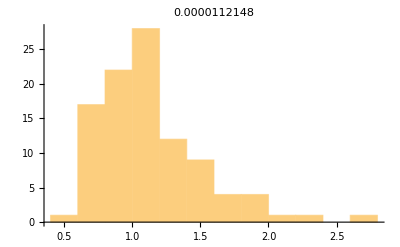
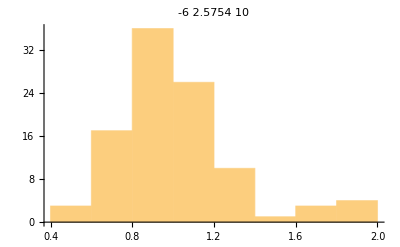
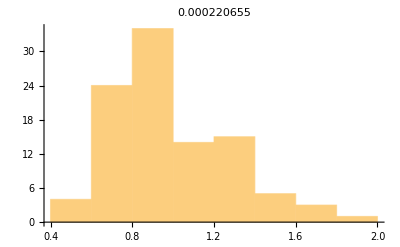
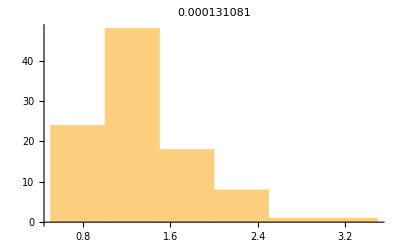
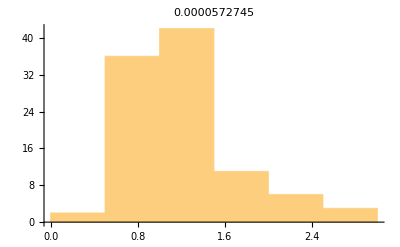
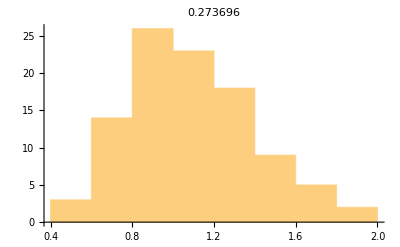
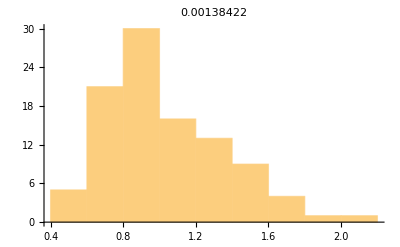
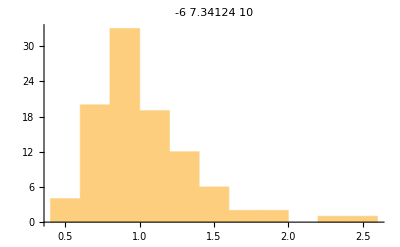
<|{0.6,0.66}→-Graphics-,{0.56,1.06}→-Graphics-,{0.98,0.82}→-Graphics-,{0.16,0.78}→-Graphics-,{0.04,0.78}→-Graphics-,{0.38,0.08}→-Graphics-,{0.98,0.98}→-Graphics-,{0.8,1.46}→-Graphics-,{0.01,0.22}→-Graphics-,{0.48,1.84}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataUnRmRNAFF[[RandomSample[Range[1,500],10]]]
```

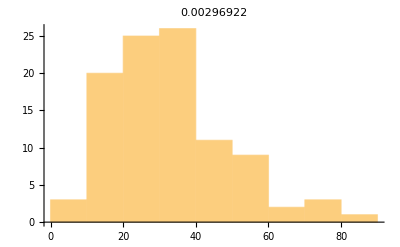
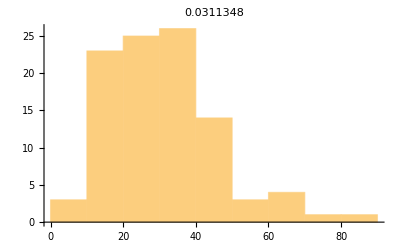
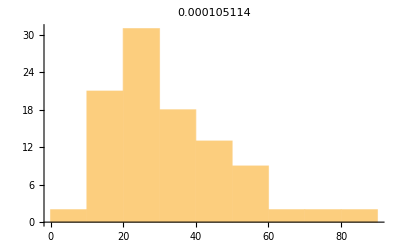
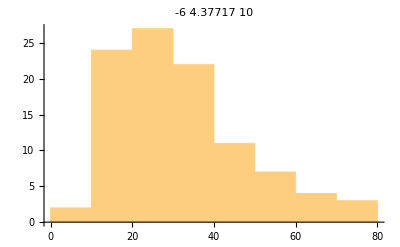
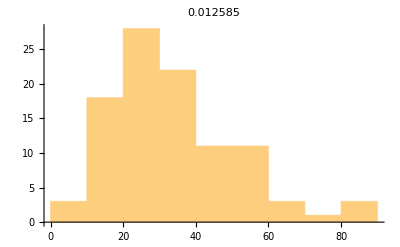
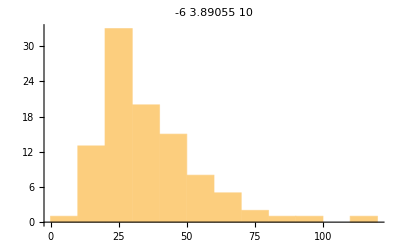
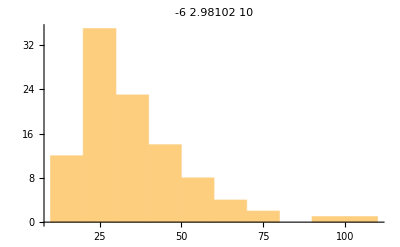
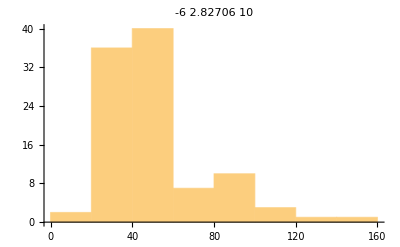
<|{0.36,1.22}→-Graphics-,{0.73,0.08}→-Graphics-,{0.84,1.52}→-Graphics-,{0.45,1.44}→-Graphics-,{0.48,1.52}→-Graphics-,{0.43,0.8}→-Graphics-,{0.38,0.64}→-Graphics-,{0.2,0.14}→-Graphics-,{0.93,1.04}→-Graphics-,{0.24,1.14}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataUnRproteinFF[[RandomSample[Range[1,500],10]]]
```

```mathematica
(*CV2*****************************************************************************************************)
```

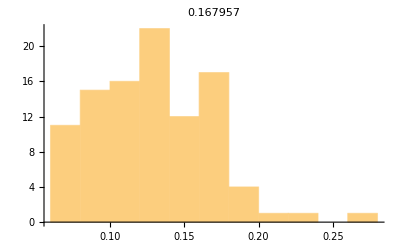
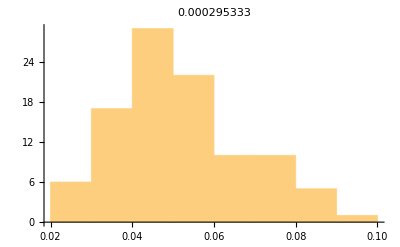
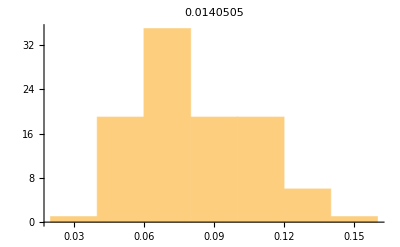
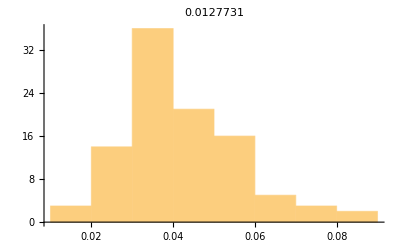
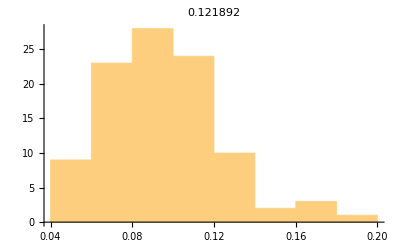
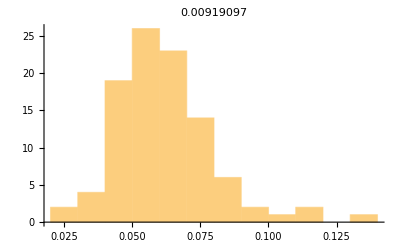
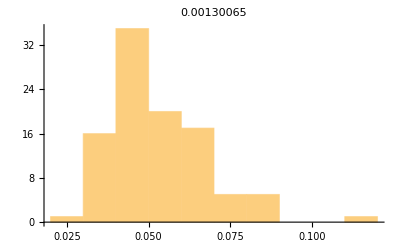
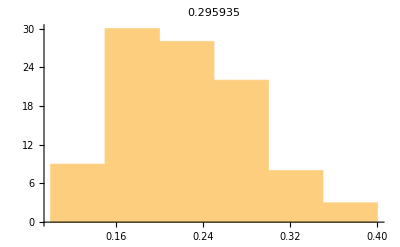
<|{0.39,1.5}→-Graphics-,{0.83,0.6}→-Graphics-,{0.49,0.8}→-Graphics-,{0.87,0.4}→-Graphics-,{0.61,1.52}→-Graphics-,{0.27,0.18}→-Graphics-,{0.56,0.42}→-Graphics-,{0.12,1.}→-Graphics-,{0.42,1.86}→-Graphics-,{0.56,1.6}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataUnRmRNACV2[[RandomSample[Range[1,500],10]]]
```

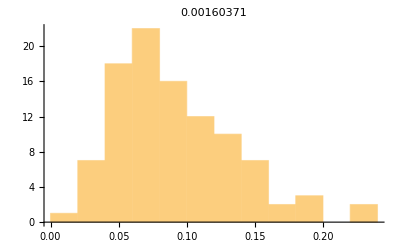
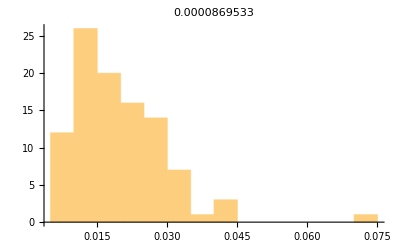
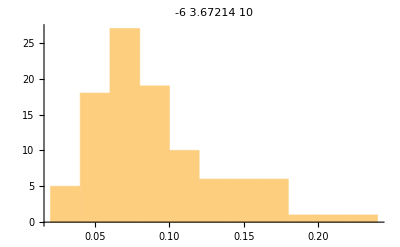
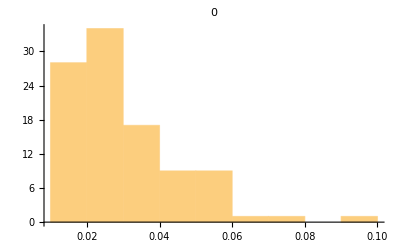
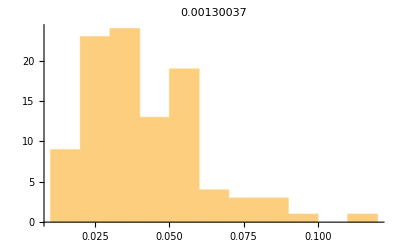
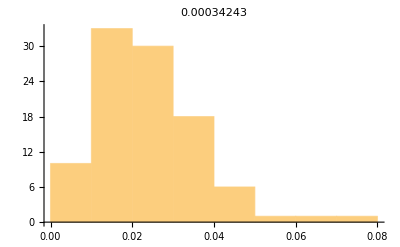
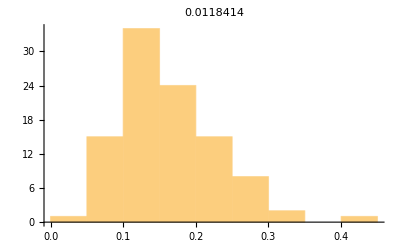
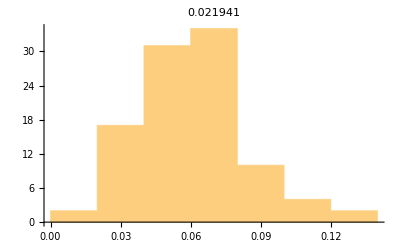
<|{0.22,1.38}→-Graphics-,{0.79,0.32}→-Graphics-,{0.26,1.84}→-Graphics-,{0.69,0.74}→-Graphics-,{0.72,1.68}→-Graphics-,{0.84,0.62}→-Graphics-,{0.07,1.38}→-Graphics-,{0.36,1.24}→-Graphics-,{0.84,1.52}→-Graphics-,{0.59,0.82}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataUnRproteinCV2[[RandomSample[Range[1,500],10]]]
```

```mathematica
(*Mean*******************************************************************************************************)
```

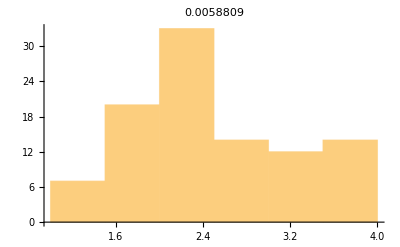
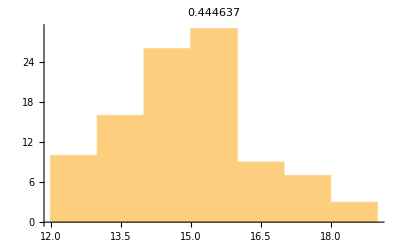
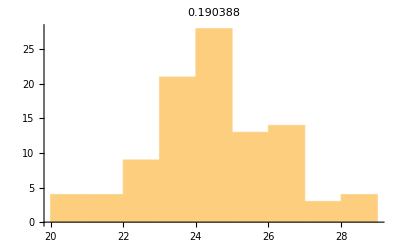
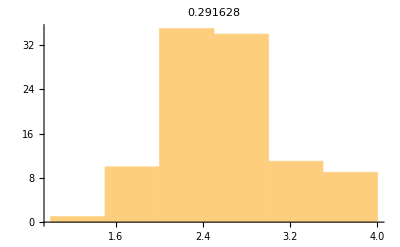
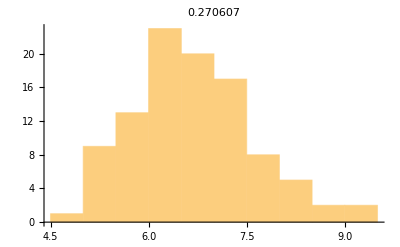
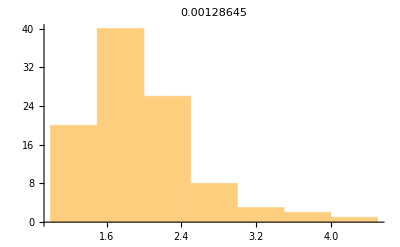
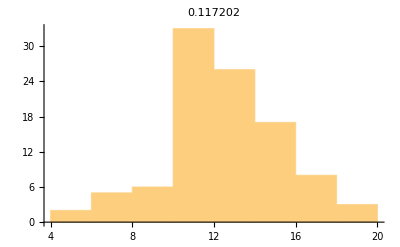
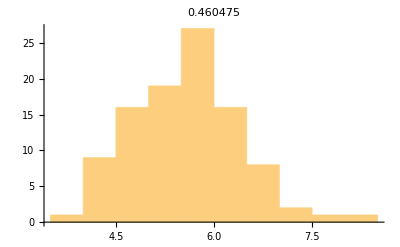
<|{0.02,0.66}→-Graphics-,{0.39,0.58}→-Graphics-,{0.58,0.26}→-Graphics-,{0.06,1.52}→-Graphics-,{0.31,1.62}→-Graphics-,{0.02,1.06}→-Graphics-,{0.03,0.08}→-Graphics-,{0.26,1.78}→-Graphics-,{0.94,0.24}→-Graphics-,{0.41,1.84}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataUnRmRNAMean[[RandomSample[Range[1,500],10]]]
```

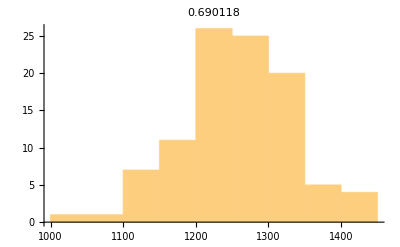
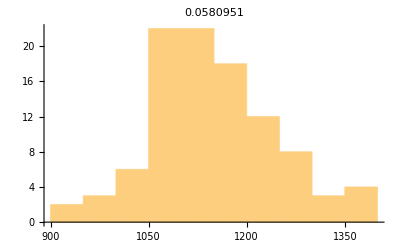
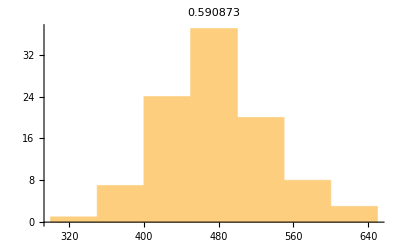
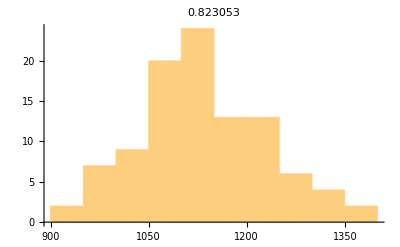
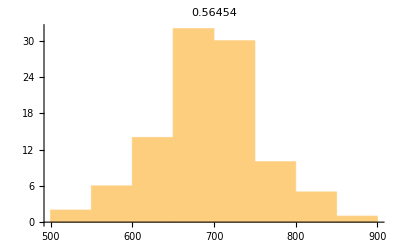
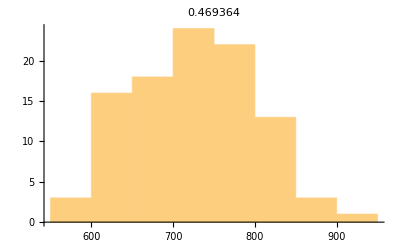
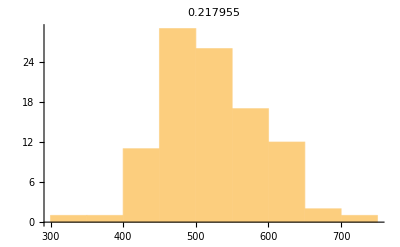
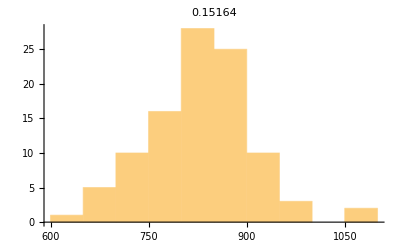
<|{0.77,0.68}→-Graphics-,{0.9,0.98}→-Graphics-,{0.41,1.84}→-Graphics-,{0.6,0.66}→-Graphics-,{0.61,1.52}→-Graphics-,{0.8,1.94}→-Graphics-,{0.36,1.4}→-Graphics-,{0.84,1.62}→-Graphics-,{0.54,0.2}→-Graphics-,{0.27,1.18}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataUnRproteinMean[[RandomSample[Range[1,500],10]]]
```

## Testing normality for dataR

```mathematica
(***Testing if the replicates are normally distribute to apply t-test dataR*)
```

```mathematica
(*FF*************************************************************************************************)
```

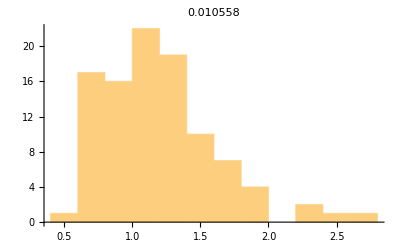
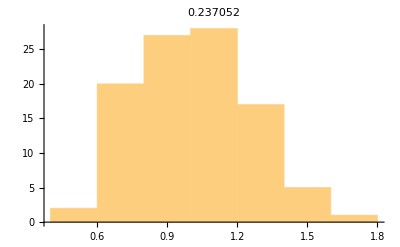
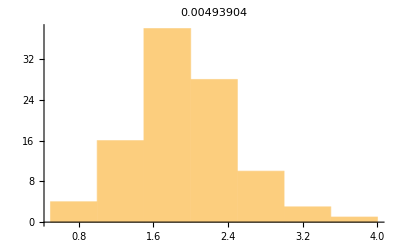
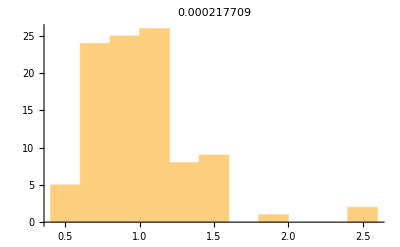
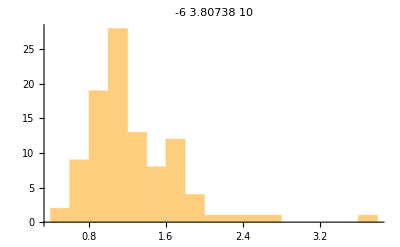
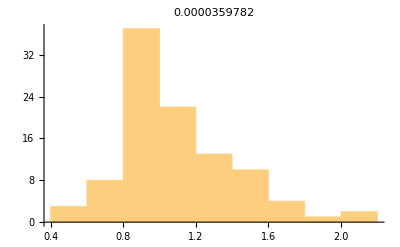
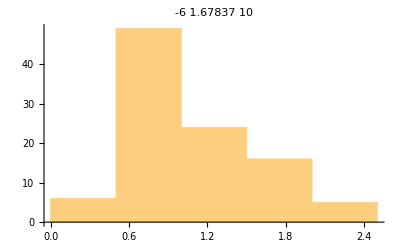
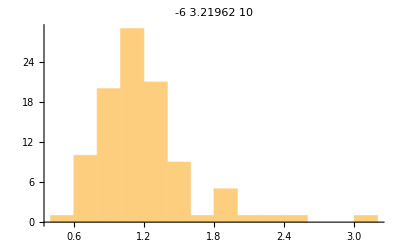
<|{0.29,0.7}→-Graphics-,{0.41,1.84}→-Graphics-,{0.08,0.28}→-Graphics-,{0.7,1.8}→-Graphics-,{0.26,0.06}→-Graphics-,{0.31,1.04}→-Graphics-,{0.02,0.66}→-Graphics-,{0.42,0.46}→-Graphics-,{0.24,1.14}→-Graphics-,{0.38,1.74}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataRmRNAFF[[RandomSample[Range[1,500],10]]]
```

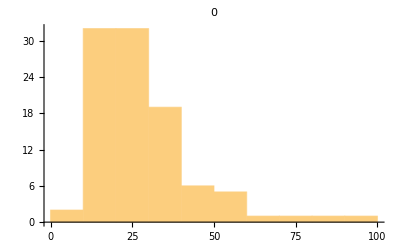
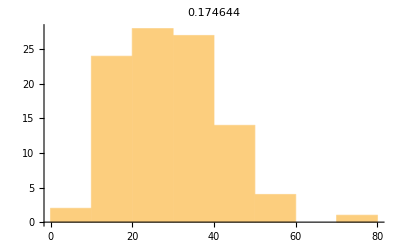
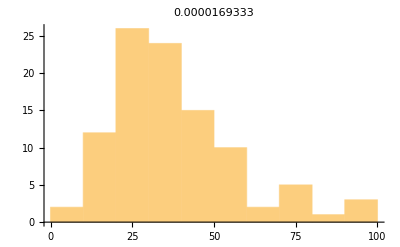
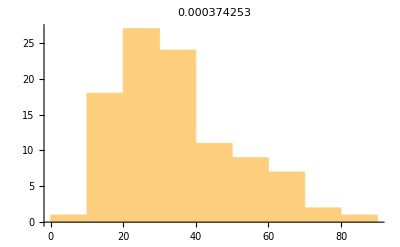
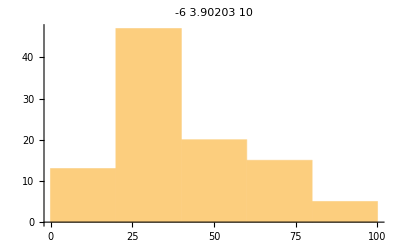
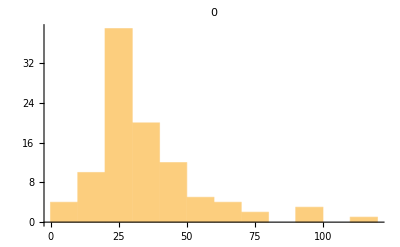
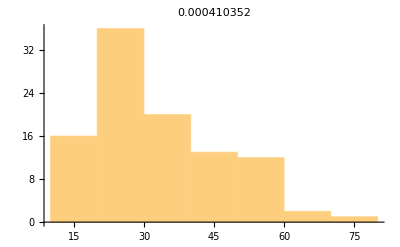
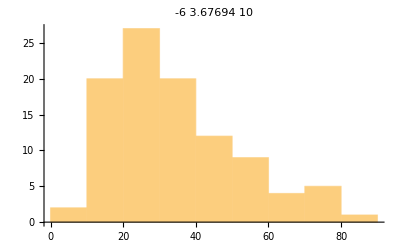
<|{0.09,1.64}→-Graphics-,{0.92,1.82}→-Graphics-,{0.31,0.54}→-Graphics-,{0.86,0.5}→-Graphics-,{0.54,0.6}→-Graphics-,{0.05,0.84}→-Graphics-,{0.42,1.86}→-Graphics-,{0.53,1.08}→-Graphics-,{0.36,1.88}→-Graphics-,{0.87,0.76}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataRproteinFF[[RandomSample[Range[1,500],10]]]
```

```mathematica
(*CV2*****************************************************************************************************)
```

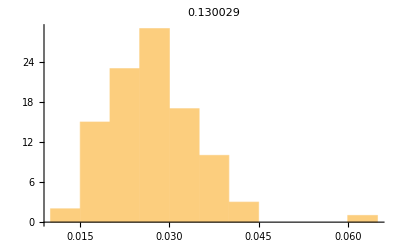
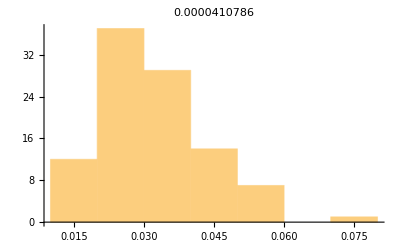
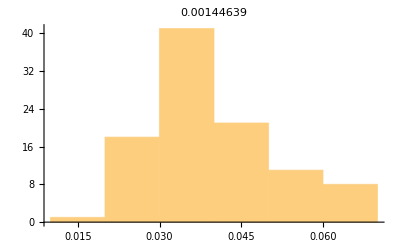
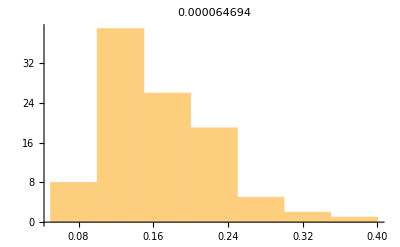
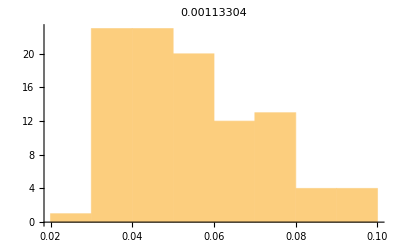
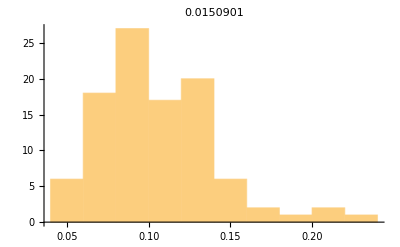
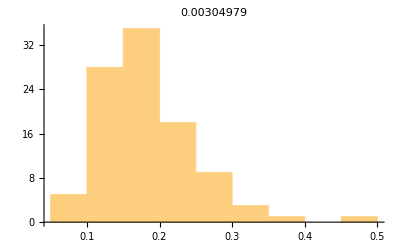
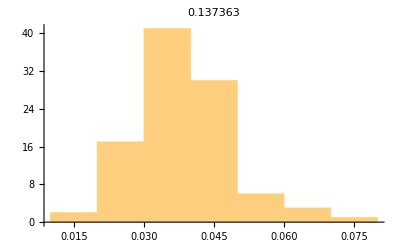
<|{0.78,0.06}→-Graphics-,{0.89,0.12}→-Graphics-,{0.33,0.08}→-Graphics-,{0.34,1.86}→-Graphics-,{0.44,0.32}→-Graphics-,{0.62,1.84}→-Graphics-,{0.27,1.88}→-Graphics-,{0.61,0.16}→-Graphics-,{0.63,0.18}→-Graphics-,{0.08,0.42}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataRmRNACV2[[RandomSample[Range[1,500],10]]]
```

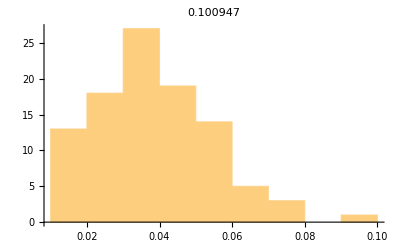
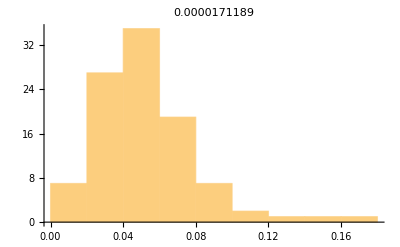
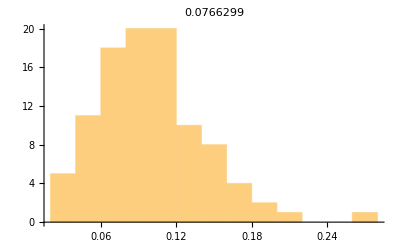
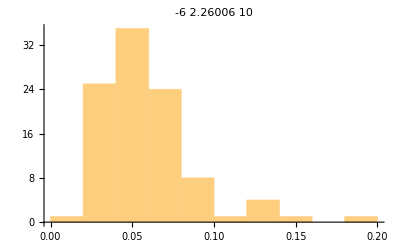
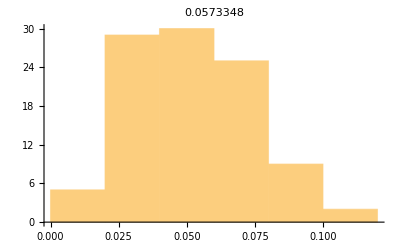
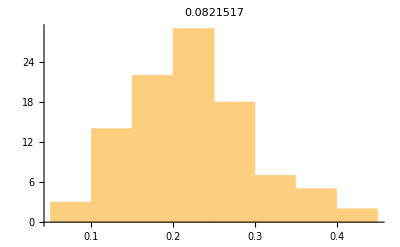
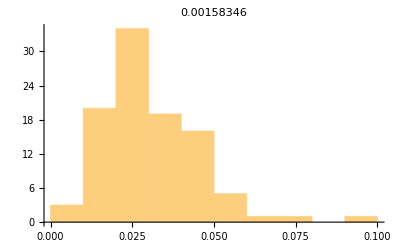
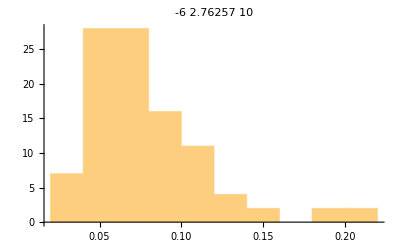
<|{0.78,1.46}→-Graphics-,{0.62,1.84}→-Graphics-,{0.25,2.}→-Graphics-,{0.47,1.88}→-Graphics-,{0.44,1.16}→-Graphics-,{0.02,1.7}→-Graphics-,{0.99,1.34}→-Graphics-,{0.33,1.8}→-Graphics-,{0.63,0.62}→-Graphics-,{0.42,0.2}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataRproteinCV2[[RandomSample[Range[1,500],10]]]
```

```mathematica
(*Mean*******************************************************************************************************)
```

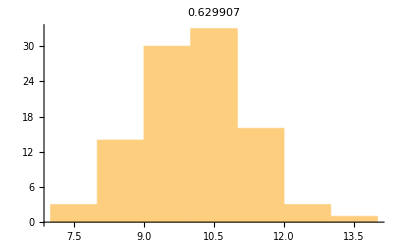
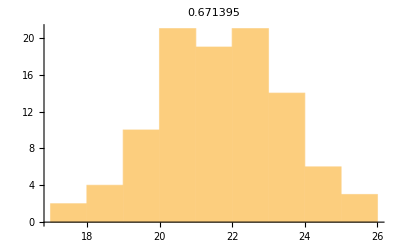
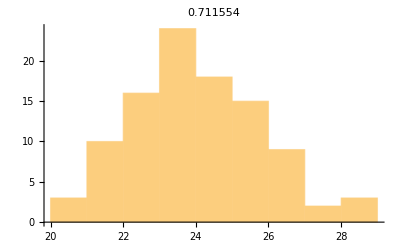
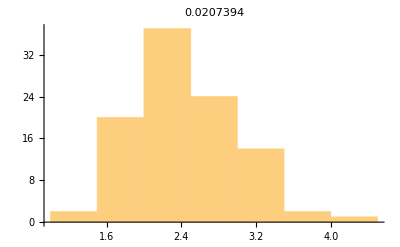
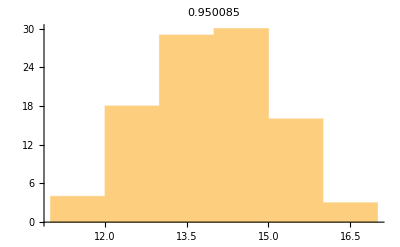
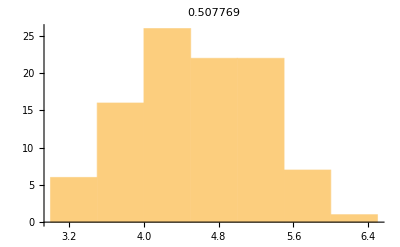
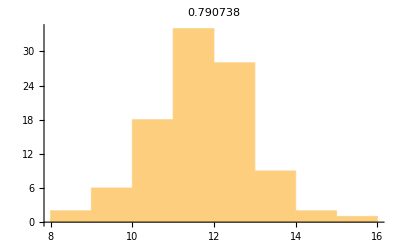
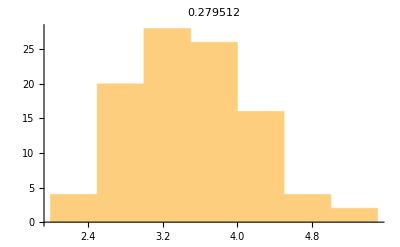
<|{0.61,1.72}→-Graphics-,{0.2,0.14}→-Graphics-,{0.6,0.28}→-Graphics-,{0.06,1.52}→-Graphics-,{0.91,1.48}→-Graphics-,{0.22,1.96}→-Graphics-,{0.91,2.}→-Graphics-,{0.09,1.36}→-Graphics-,{0.02,0.3}→-Graphics-,{0.34,1.88}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataRmRNAMean[[RandomSample[Range[1,500],10]]]
```

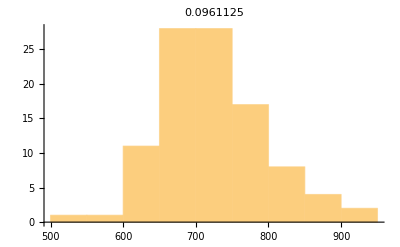
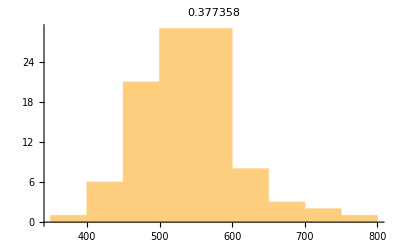
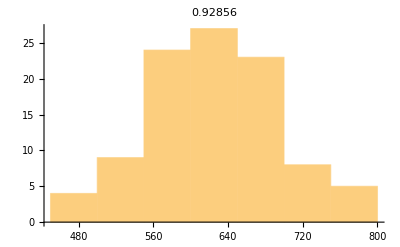
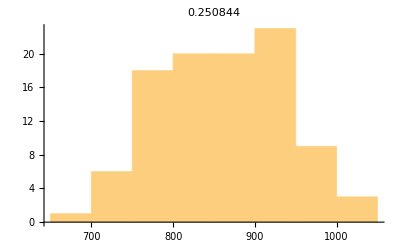
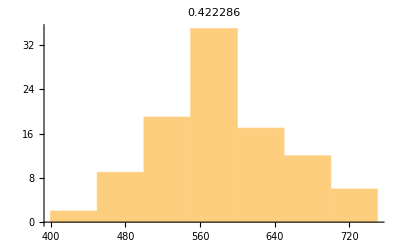
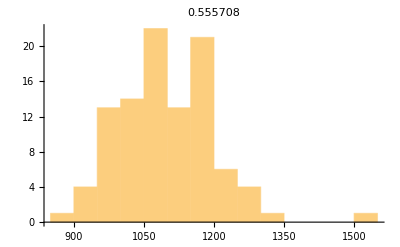
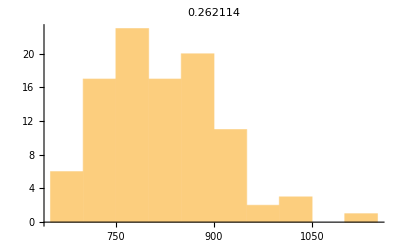
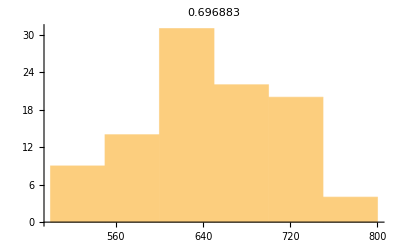
<|{0.8,1.9}→-Graphics-,{0.53,1.98}→-Graphics-,{0.52,1.56}→-Graphics-,{0.9,1.66}→-Graphics-,{0.54,1.8}→-Graphics-,{0.89,1.08}→-Graphics-,{0.33,0.66}→-Graphics-,{0.65,1.86}→-Graphics-,{0.22,0.76}→-Graphics-,{0.3,1.92}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataRproteinMean[[RandomSample[Range[1,500],10]]]
```

## Testing normality for dataAIΔA

```mathematica
(***Testing if the replicates are normally distribute to apply t-test dataR*)
```

```mathematica
(*FF*************************************************************************************************)
```

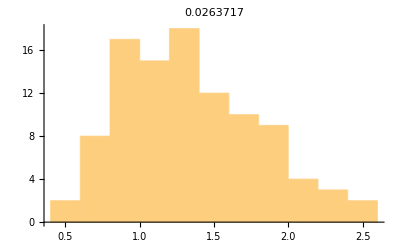
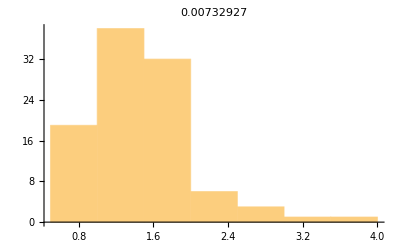
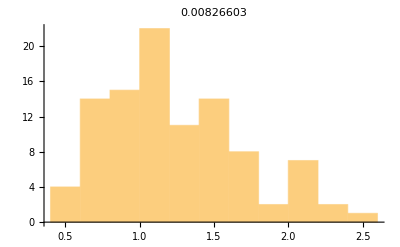
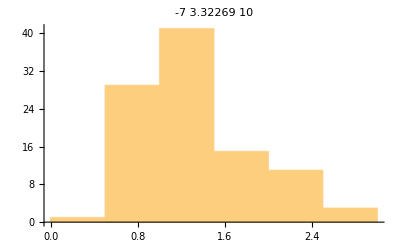
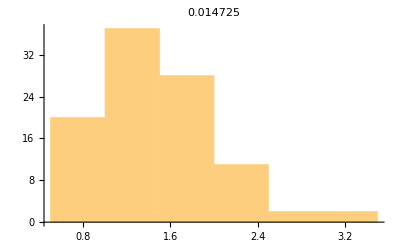
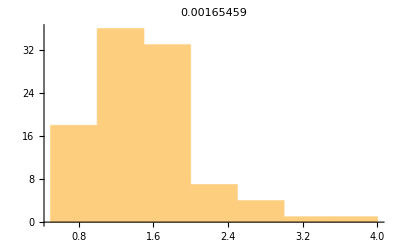
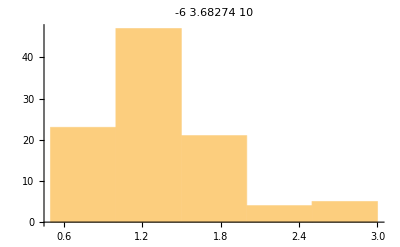
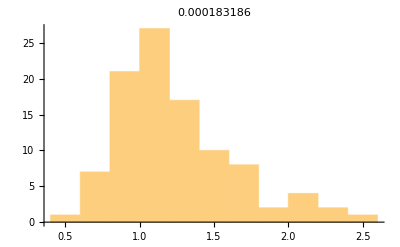
<|{0.47,0.34}→-Graphics-,{0.26,0.06}→-Graphics-,{0.87,0.4}→-Graphics-,{0.46,0.1}→-Graphics-,{0.39,0.9}→-Graphics-,{0.22,0.76}→-Graphics-,{0.67,0.62}→-Graphics-,{0.96,1.68}→-Graphics-,{0.42,1.58}→-Graphics-,{0.36,1.06}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔAAmRNAFF[[RandomSample[Range[1,500],10]]]
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔAAproteinFF[[RandomSample[Range[1,500],10]]]
```

<|{0.16,0.26}→-Graphics-,{0.04,1.12}→-Graphics-,{0.47,0.72}→-Graphics-,{0.12,1.}→-Graphics-,{0.78,0.06}→-Graphics-,{0.65,1.08}→-Graphics-,{0.54,1.12}→-Graphics-,{0.83,0.6}→-Graphics-,{0.73,0.74}→-Graphics-,{0.76,1.1}→-Graphics-|>

```mathematica
(*CV2*****************************************************************************************************)
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔAAmRNACV2[[RandomSample[Range[1,500],10]]]
```

<|{0.13,1.7}→-Graphics-,{0.34,1.88}→-Graphics-,{0.16,0.78}→-Graphics-,{0.74,1.32}→-Graphics-,{0.31,0.86}→-Graphics-,{0.26,1.06}→-Graphics-,{0.47,0.06}→-Graphics-,{0.39,1.94}→-Graphics-,{0.34,0.32}→-Graphics-,{0.23,1.58}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔAAproteinCV2[[RandomSample[Range[1,500],10]]]
```

<|{0.84,1.62}→-Graphics-,{0.38,0.08}→-Graphics-,{0.61,0.2}→-Graphics-,{0.95,0.46}→-Graphics-,{0.83,0.6}→-Graphics-,{0.33,1.8}→-Graphics-,{0.22,0.76}→-Graphics-,{0.38,0.64}→-Graphics-,{0.77,0.42}→-Graphics-,{0.07,1.04}→-Graphics-|>

```mathematica
(*Mean*******************************************************************************************************)
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔAAmRNAMean[[RandomSample[Range[1,500],10]]]
```

<|{0.26,1.26}→-Graphics-,{0.04,1.12}→-Graphics-,{0.49,0.8}→-Graphics-,{0.18,1.94}→-Graphics-,{0.16,0.26}→-Graphics-,{0.39,1.94}→-Graphics-,{0.95,0.96}→-Graphics-,{0.98,0.24}→-Graphics-,{0.46,0.1}→-Graphics-,{0.71,1.74}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔAAproteinMean[[RandomSample[Range[1,500],10]]]
```

<|{0.07,1.04}→-Graphics-,{0.49,0.98}→-Graphics-,{0.99,0.56}→-Graphics-,{0.48,1.52}→-Graphics-,{0.77,0.42}→-Graphics-,{0.9,1.}→-Graphics-,{0.47,1.74}→-Graphics-,{0.08,0.28}→-Graphics-,{0.26,1.78}→-Graphics-,{0.45,0.96}→-Graphics-|>

## Testing normality for dataAIΔI

```mathematica
(***Testing if the replicates are normally distribute to apply t-test dataR*)
```

```mathematica
(*FF*************************************************************************************************)
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIImRNAFF[[RandomSample[Range[1,500],10]]]
```

<|{0.3,1.92}→-Graphics-,{0.38,1.48}→-Graphics-,{0.6,1.56}→-Graphics-,{0.41,1.34}→-Graphics-,{0.91,2.}→-Graphics-,{0.49,1.14}→-Graphics-,{0.81,0.02}→-Graphics-,{0.02,1.7}→-Graphics-,{0.45,0.26}→-Graphics-,{0.68,1.5}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIIproteinFF[[RandomSample[Range[1,500],10]]]
```

<|{0.08,0.42}→-Graphics-,{0.48,1.84}→-Graphics-,{0.41,1.34}→-Graphics-,{0.07,1.04}→-Graphics-,{0.36,0.16}→-Graphics-,{0.33,0.66}→-Graphics-,{0.01,1.54}→-Graphics-,{0.87,1.1}→-Graphics-,{0.91,1.48}→-Graphics-,{0.98,0.24}→-Graphics-|>

```mathematica
(*CV2*****************************************************************************************************)
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIImRNACV2[[RandomSample[Range[1,500],10]]]
```

<|{0.61,1.52}→-Graphics-,{0.18,1.04}→-Graphics-,{0.99,0.44}→-Graphics-,{0.78,1.34}→-Graphics-,{0.01,0.38}→-Graphics-,{0.82,0.5}→-Graphics-,{0.85,1.66}→-Graphics-,{0.21,1.72}→-Graphics-,{0.8,0.44}→-Graphics-,{0.82,1.58}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIIproteinCV2[[RandomSample[Range[1,500],10]]]
```

<|{0.61,0.2}→-Graphics-,{0.31,0.98}→-Graphics-,{0.6,0.28}→-Graphics-,{0.94,1.42}→-Graphics-,{0.18,1.48}→-Graphics-,{0.86,0.5}→-Graphics-,{0.05,0.6}→-Graphics-,{0.59,0.02}→-Graphics-,{0.98,0.24}→-Graphics-,{0.56,1.06}→-Graphics-|>

```mathematica
(*Mean*******************************************************************************************************)
```

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIImRNAMean[[RandomSample[Range[1,500],10]]]
```

<|{0.7,0.2}→-Graphics-,{0.01,1.8}→-Graphics-,{0.68,1.88}→-Graphics-,{0.42,1.62}→-Graphics-,{0.01,1.44}→-Graphics-,{0.62,1.84}→-Graphics-,{0.21,1.26}→-Graphics-,{0.77,2.}→-Graphics-,{0.12,1.96}→-Graphics-,{0.08,1.32}→-Graphics-|>

```mathematica
Histogram[#,PlotLabel->ToString[DistributionFitTest[#]]]&/@dataAIΔIIproteinMean[[RandomSample[Range[1,500],10]]]
```

<|{0.41,1.2}→-Graphics-,{0.73,0.6}→-Graphics-,{0.85,1.66}→-Graphics-,{0.52,1.76}→-Graphics-,{0.59,0.84}→-Graphics-,{0.82,1.58}→-Graphics-,{0.18,0.58}→-Graphics-,{0.29,0.98}→-Graphics-,{0.78,0.96}→-Graphics-,{0.51,0.78}→-Graphics-|>

## Plots

```mathematica
plotsUnR={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
□plotsR={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
plotAIΔAA={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
plotAIΔII={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

## Comparing dataUnR with dataR

```mathematica
(***************data no es normal- no funcion t-teest*)
```

```mathematica
TTest[{dataUnRmRNAFF[[#]],dataRmRNAFF[[#]]}]&/@Range[1,500]
```

TTest::nortst: At least one of the p-values in {0.118266,3.83062×10^-6}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.00222526,9.43039×10^-7}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.0000478245,0.0156963}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

{0.426653,0.877624,0.788865,0.361468,0.398166,0.17654,0.374628,0.567686,0.142362,0.949386,0.913647,0.94917,0.896583,0.41836,0.171253,0.214737,0.836614,0.604127,0.05671,0.54497,0.268753,0.847127,0.19026,0.385547,0.687144,0.118365,0.640783,0.895521,0.366696,0.0251256,0.141965,0.369025,0.237961,0.239173,0.984474,0.437133,0.086213,0.0839719,0.690958,0.382978,0.455961,0.753768,0.25293,0.741134,0.987393,0.44978,0.817947,0.531893,0.214204,0.823287,0.0918734,0.410144,0.4632,0.894935,0.115411,0.379501,0.462752,0.324091,0.823251,0.260727,0.866493,0.408774,0.194281,0.513477,0.275166,0.235394,0.382068,0.400503,0.0969789,0.400906,0.723706,0.363195,0.777994,0.335425,0.899567,0.592822,0.496752,0.822684,0.260162,0.312459,0.901268,0.789327,0.312188,0.972882,0.0918389,0.544021,0.539629,0.107475,0.514293,0.344785,0.744739,0.00485184,0.392228,0.176318,0.490835,0.620146,0.522473,0.270618,0.721932,0.559219,0.130137,0.386939,0.890003,0.907894,0.280571,0.0500501,0.510166,0.0151254,0.987346,0.300905,0.838164,0.6975,0.484241,0.97299,0.709098,0.300024,0.929479,0.998437,0.437063,0.333759,0.70239,0.771769,0.787587,0.55717,0.614958,0.869446,0.936615,0.346891,0.721316,0.835619,0.431755,0.50288,0.510819,0.276397,0.731733,0.600248,0.396987,0.524867,0.790999,0.140318,0.53412,0.853295,0.846583,0.237609,0.11986,0.300646,0.614264,0.607294,0.483895,0.0291735,0.587294,0.831361,0.209659,0.472873,0.494768,0.36339,0.0178616,0.969802,0.973489,0.744906,0.450594,0.521247,0.951724,0.533979,0.972314,0.374037,0.761466,0.24833,0.86275,0.730882,0.443228,0.060171,0.014083,0.448662,0.493574,0.666261,0.628552,0.0453576,0.884227,0.166779,0.450603,0.250051,0.0201962,0.406568,0.109476,0.247617,0.299877,0.749742,0.867359,0.390438,0.0463464,0.656891,0.572486,0.608506,0.791528,0.714202,0.659507,0.40944,0.164144,0.196198,0.652187,0.724519,0.639063,0.04395,0.911878,0.180849,0.638785,0.256557,0.439026,0.188302,0.0445247,0.215377,0.010354,0.0114344,0.804763,0.421528,0.000329564,0.645033,0.536501,0.267864,0.211407,0.965614,0.446771,0.873509,0.78929,0.706972,0.406996,0.955238,0.543438,0.839585,0.397476,0.292014,0.0380534,0.0790943,0.800022,0.0593674,0.619027,0.392045,0.237195,0.678372,0.0743066,0.67758,0.782821,0.787314,0.181051,0.985238,0.875083,0.933849,0.730468,0.408106,0.524613,0.976548,0.368114,0.858342,0.887876,0.610432,0.586904,0.964663,0.742845,0.314663,0.289216,0.227568,0.76764,0.609541,0.163053,0.618535,0.897365,0.284043,0.0451162,0.486687,0.123392,0.594138,0.0000314409,0.649384,0.987158,0.295516,0.511669,0.520509,0.863874,0.364503,0.232192,0.675628,0.787729,0.854659,0.20858,0.170708,0.459822,0.718007,0.0815628,0.236268,0.520289,0.986483,0.0546517,0.0839662,0.108293,0.889697,0.978985,0.0669313,0.0594381,0.493937,0.814999,0.0848745,0.595922,0.74787,0.691422,0.94171,0.975654,0.356616,0.799789,0.910539,0.93596,0.80613,0.965482,0.524519,0.204334,0.557512,0.573743,0.486501,0.626972,0.450008,0.384966,0.909517,0.19213,0.705943,0.957416,0.0385945,0.624176,0.0160866,0.658144,0.49206,0.426026,0.636994,0.317424,0.92524,0.0314787,0.870759,0.867043,0.030527,0.0608853,0.147441,0.130213,0.768505,0.71193,0.552438,0.906798,0.651588,0.590661,0.967751,0.0723409,0.427717,0.3309,0.977757,0.269147,0.69937,0.482505,0.417717,0.318503,0.829833,0.86342,0.458714,0.811169,0.583599,0.504106,0.937819,0.215854,0.992311,0.751893,0.244689,0.728756,0.579212,0.703558,0.314235,0.139576,0.434324,0.583253,0.533468,0.64478,0.359002,0.718583,0.725467,0.864321,0.778564,0.412368,0.293563,0.787774,0.497921,0.0872728,0.344211,0.466178,0.406735,0.120394,0.47405,0.573437,0.152751,0.576997,0.401381,0.222307,0.367113,0.659601,0.249368,0.137257,0.749329,0.599732,0.618037,0.986548,0.33365,0.204258,0.0549059,0.418769,0.40009,0.195422,0.949796,0.210171,0.985619,0.751823,0.444174,0.00251534,0.0442419,0.813674,0.000528385,0.0807124,0.934987,0.79952,0.357717,0.138008,0.764409,0.157599,0.605119,0.996789,0.217629,0.447778,0.273628,0.894941,0.336389,0.449277,0.520681,0.97406,0.127171,0.281967,0.498935,0.957399,0.288681,0.419432,0.399638,0.705418,0.313863,0.265424,0.176187,0.848343,0.799273,0.79514,0.351316,0.678239,0.570793,0.390014,0.528162,0.723609,0.0448566,0.310854,0.523418,0.529859,0.443563,0.937506,0.893946,0.945061,0.77506,0.448877,0.245626,0.459813,0.0110401,0.0754658,0.859459,0.261736,0.834905,0.643855,0.470951,0.734671,0.0932568,0.139345,0.382817,0.968894,0.538217,0.451126,0.104217,0.370716,0.0353504,0.363119,0.882578,0.571858,0.0933881,0.75947,0.787134,0.0186598,0.97385,0.285057,0.147048,0.427729,0.237512,0.115077,0.0845678}

```mathematica
Length[Flatten[sample[[1;;5]],1]]
```

500

```mathematica
(************MannWhitneyTest is equal to the Wilcoxon para muestras no pareadas - pareado es que cada punto de la muestra uno se relaciona con un punto de la muestra dos. En este caso no son pareadas porque ambas muestras son las replicas aleatorias de un set de parámetros*)
```

```mathematica
,
```

```mathematica
GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataUnRproteinMean[[#]],dataRproteinMean[[#]]}]&/@Range[1,500]}]//Association,#>0.05&]
```

<|True→<|{0.06,0.06}→0.645101,{0.01,0.38}→0.107623,{0.05,0.74}→0.678761,{0.07,0.9}→0.344981,{0.02,1.06}→0.260513,{0.02,1.56}→0.371826,{0.1,1.74}→0.760974,{0.04,1.9}→0.573298,{0.19,0.04}→0.183378,{0.18,0.4}→0.545353,{0.18,0.58}→0.0577895,{0.14,0.7}→0.405424,{0.2,1.14}→0.813598,{0.18,1.32}→0.214968,{0.16,1.44}→0.490032,{0.2,1.74}→0.479342,{0.18,1.9}→0.550235,{0.24,0.18}→0.480861,{0.29,0.3}→0.563358,{0.21,0.5}→0.245304,{0.23,0.7}→0.118735,{0.28,0.84}→0.643348,{0.22,1.38}→0.975635,{0.29,1.44}→0.352522,{0.24,1.78}→0.775909,{0.22,1.96}→0.283978,{0.38,0.12}→0.874773,{0.4,0.22}→0.813598,{0.33,0.58}→0.344981,{0.38,0.64}→0.0638379,{0.35,0.86}→0.142307,{0.31,1.04}→0.942538,{0.39,1.3}→0.859394,{0.39,1.52}→0.886339,{0.39,1.64}→0.865155,{0.34,1.88}→0.867077,{0.5,0.12}→0.452447,{0.44,0.32}→0.25742,{0.48,0.54}→0.446588,{0.47,0.72}→0.343734,{0.48,0.94}→0.221361,{0.41,1.2}→0.989278,{0.47,1.38}→0.736897,{0.42,1.58}→0.886339,{0.48,1.76}→0.337544,{0.47,1.88}→0.0920433,{0.58,0.2}→0.571635,{0.58,0.26}→0.218605,{0.59,0.52}→0.985379,{0.55,0.74}→0.798465,{0.6,0.86}→0.252322,{0.54,1.04}→0.223213,{0.58,1.38}→0.366615,{0.52,1.56}→0.915354,{0.57,1.8}→0.736897,{0.56,1.94}→0.716722,{0.66,0.38}→0.503963,{0.65,0.56}→0.169316,{0.68,0.64}→0.14364,{0.66,0.82}→0.464294,{0.66,1.18}→0.751685,{0.7,1.32}→0.453918,{0.61,1.52}→0.0988388,{0.7,1.8}→0.508653,{0.65,1.86}→0.790927,{0.73,0.08}→0.872848,{0.79,0.32}→0.50085,{0.8,0.44}→0.111414,{0.75,0.82}→0.405424,{0.76,1.02}→0.934763,{0.78,1.34}→0.367913,{0.71,1.6}→0.272072,{0.78,1.66}→0.872848,{0.78,2.}→0.919232,{0.81,0.02}→0.749831,{0.88,0.3}→0.211375,{0.83,0.6}→0.429273,{0.89,0.66}→0.913416,{0.9,1.}→0.870924,{0.89,1.08}→0.124021,{0.87,1.38}→0.151147,{0.83,1.46}→0.867077,{0.84,1.62}→0.430701,{0.81,1.82}→0.823092,{1.,0.02}→0.387732,{0.98,0.24}→0.149761,{0.99,0.56}→0.905668,{0.98,0.8}→0.551867,{0.98,0.82}→0.373136,{0.98,1.1}→0.838336,{0.93,1.22}→0.762836,{0.97,1.56}→0.718548,{0.97,1.66}→0.58668,{1.,2.}→0.488497,{0.05,0.2}→0.584999,{0.02,0.3}→0.216781,{0.05,0.58}→0.815495,{0.02,0.66}→0.538877,{0.05,0.84}→0.320594,{0.05,1.08}→0.907604,{0.09,1.36}→0.320594,{0.09,1.66}→0.579971,{0.07,1.96}→0.785285,{0.2,0.14}→0.991227,{0.17,0.24}→0.338776,{0.13,0.5}→0.545353,{0.17,0.66}→0.622477,{0.16,0.94}→0.694937,{0.18,1.16}→0.845981,{0.19,1.38}→0.514941,{0.18,1.52}→0.811702,{0.13,1.7}→0.144311,{0.18,1.94}→0.290619,{0.27,0.18}→0.177025,{0.3,0.6}→0.46878,{0.22,0.76}→0.68773,{0.29,0.9}→0.565009,{0.24,1.18}→0.73874,{0.23,1.58}→0.923112,{0.26,1.74}→0.1604,{0.26,1.84}→0.312332,{0.39,0.18}→0.662732,{0.34,0.32}→0.423589,{0.31,0.54}→0.807915,{0.34,0.68}→0.362737,{0.31,0.98}→0.131978,{0.34,1.1}→0.311163,{0.36,1.22}→0.508653,{0.35,1.48}→0.645101,{0.31,1.62}→0.682343,{0.39,1.94}→0.794693,{0.47,0.06}→0.919232,{0.43,0.36}→0.473291,{0.41,0.52}→0.925053,{0.49,0.8}→0.49157,{0.45,0.96}→0.535653,{0.44,1.16}→0.0934669,{0.48,1.32}→0.496198,{0.48,1.52}→0.813598,{0.49,1.62}→0.389076,{0.42,1.86}→0.112517,{0.55,0.02}→0.480861,{0.6,0.28}→0.684137,{0.54,0.6}→0.119894,{0.51,0.78}→0.579971,{0.6,0.98}→0.264676,{0.51,1.2}→0.806022,{0.56,1.24}→0.703985,{0.56,1.6}→0.36145,{0.51,1.88}→0.610439,{0.61,0.16}→0.0915726,{0.67,0.22}→0.568317,{0.65,0.58}→0.295103,{0.67,0.62}→0.197437,{0.65,0.94}→0.28618,{0.63,1.18}→0.453918,{0.65,1.32}→0.452447,{0.68,1.5}→0.830706,{0.7,1.68}→0.720376,{0.67,1.94}→0.940594,{0.77,0.06}→0.212269,{0.77,0.32}→0.303062,{0.76,0.44}→0.772167,{0.76,0.8}→0.560063,{0.78,0.96}→0.886339,{0.73,1.08}→0.707616,{0.74,1.32}→0.540492,{0.77,1.44}→0.999025,{0.75,1.68}→0.17391,{0.89,0.12}→0.358885,{0.85,0.28}→0.636359,{0.89,0.5}→0.455392,{0.86,0.68}→0.913416,{0.9,0.98}→0.627667,{0.87,1.1}→0.145659,{0.88,1.4}→0.956157,{0.84,1.52}→0.519684,{0.9,1.66}→0.106029,{0.86,1.92}→0.909541,{0.93,0.1}→0.166303,{0.94,0.38}→0.0816986,{0.95,0.66}→0.823092,{0.98,0.98}→0.225075,{0.98,1.14}→0.210484,{0.99,1.34}→0.319405,{0.94,1.42}→0.230729,{0.92,1.74}→0.318219,{0.96,1.98}→0.483908,{0.09,0.1}→0.948373,{0.08,0.24}→0.52127,{0.09,0.5}→0.969789,{0.09,0.68}→0.684137,{0.08,0.9}→0.57663,{0.04,1.04}→0.93865,{0.08,1.36}→0.0856282,{0.09,1.64}→0.857475,{0.11,0.04}→0.347483,{0.16,0.36}→0.638103,{0.19,0.48}→0.746128,{0.16,0.78}→0.702172,{0.12,1.}→0.946428,{0.18,1.12}→0.485435,{0.19,1.28}→0.804131,{0.19,1.52}→0.744279,{0.13,1.72}→0.806022,{0.19,1.94}→0.65919,{0.22,0.18}→0.415147,{0.26,0.3}→0.733214,{0.25,0.58}→0.331425,{0.29,0.7}→0.880553,{0.23,0.86}→0.197437,{0.24,1.14}→0.137067,{0.26,1.26}→0.952265,{0.23,1.56}→0.401299,{0.29,1.72}→0.435001,{0.3,1.92}→0.129488,{0.36,0.16}→0.494653,{0.32,0.3}→0.565009,{0.38,0.52}→0.63985,{0.37,0.76}→0.228834,{0.39,0.9}→0.736897,{0.36,1.06}→0.307674,{0.36,1.4}→0.370519,{0.39,1.5}→0.181774,{0.31,1.7}→0.225075,{0.36,1.88}→0.598506,{0.41,0.2}→0.413749,{0.47,0.34}→0.364027,{0.41,0.58}→0.479342,{0.48,1.}→0.148384,{0.44,1.18}→0.195743,{0.42,1.28}→0.102898,{0.45,1.44}→0.631138,{0.47,1.74}→0.714897,{0.48,1.84}→0.645101,{0.56,0.18}→0.131978,{0.52,0.32}→0.783407,{0.56,0.42}→0.556777,{0.54,0.7}→0.600204,{0.59,0.82}→0.888269,{0.54,1.12}→0.657422,{0.57,1.26}→0.905668,{0.57,1.42}→0.319405,{0.52,1.76}→0.430701,{0.53,1.98}→0.382384,{0.65,0.28}→0.410963,{0.63,0.48}→0.558419,{0.61,0.7}→0.420764,{0.7,0.98}→0.51652,{0.65,1.04}→0.427848,{0.65,1.22}→0.777781,{0.65,1.44}→0.0834266,{0.61,1.64}→0.225075,{0.69,1.9}→0.370519,{0.78,0.06}→0.553501,{0.74,0.32}→0.467282,{0.73,0.6}→0.65213,{0.77,0.68}→0.253336,{0.79,0.88}→0.645101,{0.78,1.1}→0.669837,{0.74,1.4}→0.669837,{0.8,1.46}→0.429273,{0.71,1.74}→0.427848,{0.79,1.96}→0.0915726,{0.9,0.12}→0.490032,{0.87,0.24}→0.237452,{0.84,0.58}→0.729538,{0.84,0.62}→0.600204,{0.83,0.98}→0.869,{0.9,1.06}→0.514941,{0.82,1.3}→0.627667,{0.87,1.5}→0.720376,{0.85,1.66}→0.789045,{0.81,1.84}→0.357606,{0.93,0.16}→0.859394,{0.94,0.24}→0.958104,{0.99,0.44}→0.0787444,{0.95,0.96}→0.967841,{0.94,1.1}→0.583321,{0.91,1.22}→0.226011,{0.92,1.48}→0.199998,{0.96,1.68}→0.290619,{0.91,2.}→0.669837,{0.07,0.02}→0.239398,{0.08,0.28}→0.915354,{0.08,0.42}→0.225075,{0.1,0.64}→0.573298,{0.09,1.}→0.398563,{0.04,1.12}→0.410963,{0.06,1.3}→0.426426,{0.08,1.54}→0.44513,{0.02,1.7}→0.867077,{0.06,1.9}→0.555138,{0.13,0.16}→0.757254,{0.16,0.26}→0.25742,{0.11,0.48}→0.975635,{0.12,0.72}→0.256395,{0.15,0.98}→0.149761,{0.18,1.04}→0.894063,{0.12,1.28}→0.164071,{0.14,1.46}→0.355058,{0.12,1.62}→0.461316,{0.12,2.}→0.607019,{0.25,0.02}→0.0600825,{0.28,0.34}→0.537264,{0.23,0.5}→0.198288,{0.26,0.78}→0.315855,{0.26,1.}→0.789045,{0.26,1.06}→0.139014,{0.3,1.22}→0.993177,{0.27,1.6}→0.200857,{0.21,1.72}→0.307674,{0.27,1.88}→0.425006,{0.38,0.08}→0.430701,{0.35,0.22}→0.631138,{0.36,0.48}→0.857475,{0.39,0.78}→0.561709,{0.31,0.86}→0.112517,{0.31,1.18}→0.888269,{0.35,1.3}→0.779655,{0.38,1.48}→0.722205,{0.33,1.8}→0.847894,{0.34,1.86}→0.377082,{0.42,0.2}→0.952265,{0.41,0.4}→0.0531202,{0.42,0.46}→0.612153,{0.47,0.68}→0.956157,{0.43,0.96}→0.497746,{0.49,1.14}→0.727703,{0.41,1.34}→0.882481,{0.44,1.64}→0.496198,{0.41,1.9}→0.324179,{0.54,0.2}→0.252322,{0.58,0.4}→0.494653,{0.57,0.58}→0.224143,{0.52,0.8}→0.952265,{0.55,0.98}→0.75354,{0.53,1.08}→0.73874,{0.52,1.28}→0.0688957,{0.6,1.56}→0.187434,{0.54,1.8}→0.870924,{0.57,1.88}→0.240376,{0.61,0.2}→0.255372,{0.62,0.28}→0.965893,{0.67,0.46}→0.997076,{0.69,0.74}→0.401299,{0.7,0.94}→0.605312,{0.64,1.2}→0.437881,{0.63,1.26}→0.571635,{0.7,1.46}→0.244313,{0.61,1.72}→0.787165,{0.62,1.84}→0.0624504,{0.77,0.18}→0.583321,{0.8,0.28}→0.326583,{0.75,0.52}→0.65213,{0.73,0.74}→0.54211,{0.8,0.84}→0.673401,{0.77,1.02}→0.740585,{0.79,1.26}→0.401299,{0.74,1.52}→0.232636,{0.72,1.68}→0.869,{0.86,0.02}→0.796579,{0.83,0.3}→0.969789,{0.82,0.5}→0.422175,{0.87,0.76}→0.98343,{0.85,0.98}→0.116444,{0.86,1.14}→0.107623,{0.83,1.38}→0.285077,{0.82,1.58}→0.172369,{0.83,1.68}→0.625935,{0.85,1.94}→0.322981,{0.99,0.06}→0.960051,{0.93,0.24}→0.849809,{0.95,0.46}→0.107623,{0.99,0.76}→0.128872,{1.,0.82}→0.960051,{0.93,1.04}→0.709434,{0.97,1.32}→0.69133,{0.92,1.46}→0.744279,{0.97,1.78}→0.325379,{0.92,1.82}→0.762836,{0.03,0.08}→0.790927,{0.01,0.22}→0.802241,{0.06,0.52}→0.402671,{0.04,0.78}→0.256395,{0.1,0.84}→0.600204,{0.08,1.32}→0.583321,{0.01,1.54}→0.497746,{0.01,1.8}→0.673401,{0.04,1.98}→0.823092,{0.13,0.04}→0.696743,{0.16,0.24}→0.556777,{0.2,0.42}→0.0988388,{0.14,0.76}→0.483908,{0.18,0.86}→0.921172,{0.13,1.1}→0.645101,{0.2,1.38}→0.319405,{0.18,1.48}→0.125823,{0.2,1.8}→0.709434,{0.12,1.96}→0.171601,{0.26,0.06}→0.399929,{0.29,0.28}→0.198288,{0.28,0.58}→0.849809,{0.23,0.64}→0.546978,{0.29,0.98}→0.439326,{0.27,1.18}→0.804131,{0.29,1.3}→0.244313,{0.29,1.48}→0.36145,{0.26,1.78}→0.44513,{0.25,2.}→0.631138,{0.33,0.08}→0.772167,{0.33,0.36}→0.401299,{0.39,0.58}→0.0944258,{0.33,0.66}→0.919232,{0.34,0.98}→0.999025,{0.33,1.04}→0.165557,{0.36,1.24}→0.315855,{0.38,1.74}→0.243324,{0.36,1.96}→0.899863,{0.46,0.1}→0.483908,{0.45,0.26}→0.790927,{0.47,0.6}→0.535653,{0.45,0.64}→0.331425,{0.49,0.98}→0.749831,{0.46,1.18}→0.180976,{0.41,1.38}→0.266775,{0.43,1.52}→0.4748,{0.42,1.62}→0.391772,{0.41,1.84}→0.146336,{0.59,0.02}→0.625935,{0.56,0.56}→0.969789,{0.6,0.66}→0.0692692,{0.59,0.84}→0.20345,{0.56,1.06}→0.774037,{0.53,1.5}→0.25742,{0.54,1.74}→0.327789,{0.56,1.98}→0.511792,{0.63,0.18}→0.907604,{0.7,0.34}→0.98343,{0.63,0.56}→0.735055,{0.63,0.62}→0.238424,{0.67,0.88}→0.242339,{0.65,1.08}→0.192388,{0.66,1.32}→0.156792,{0.65,1.42}→0.473291,{0.62,1.72}→0.645101,{0.68,1.88}→0.269945,{0.73,0.02}→0.755396,{0.77,0.26}→0.823092,{0.77,0.42}→0.366615,{0.74,0.74}→0.184993,{0.77,0.94}→0.167804,{0.76,1.1}→0.894063,{0.77,1.28}→0.0911039,{0.78,1.46}→0.631138,{0.72,1.74}→0.175462,{0.77,2.}→0.591735,{0.87,0.06}→0.0953926,{0.87,0.4}→0.448049,{0.86,0.5}→0.693133,{0.86,0.66}→0.0666891,{0.85,0.9}→0.979532,{0.85,1.06}→0.93282,{0.83,1.24}→0.340011,{0.86,1.5}→0.804131,{0.89,1.72}→0.17391,{0.95,0.02}→0.75354,{0.97,0.4}→0.0617661,{0.91,0.54}→0.272072,{0.91,0.76}→0.154657,{0.97,1.}→0.151844,{0.93,1.1}→0.973686,{0.93,1.38}→0.408188,{0.91,1.48}→0.807915,{0.93,1.8}→0.612153,{0.98,1.96}→0.7647|>,False→<|{0.05,0.6}→0.00561284,{0.07,1.38}→0.00169796,{0.15,1.}→0.00528501,{0.25,1.12}→0.0370301,{0.7,0.2}→0.0284881,{0.73,0.78}→0.0496156,{0.01,1.44}→0.0031989,{0.25,0.26}→0.0297506,{0.21,1.26}→0.0122211,{0.55,1.72}→0.00811105,{0.8,1.9}→0.027443,{0.91,0.56}→0.0109344,{0.06,1.52}→0.0449844,{0.04,1.92}→0.00436899,{0.43,0.8}→0.00365601,{0.66,0.02}→0.0290234,{0.97,0.66}→0.0259373,{0.45,1.52}→0.0149994,{0.8,1.94}→0.0169213,{0.07,1.04}→0.0484914,{0.34,1.56}→0.0251321,{0.54,0.28}→0.0386091,{0.52,1.32}→0.0426838,{0.87,1.88}→0.0185624|>|>

```mathematica
MapAt[Reverse,%//Values//Keys,{All,All}]
```

{{{0.06,0.06},{0.38,0.01},{0.6,0.05},{0.74,0.05},{0.9,0.07},{1.06,0.02},{1.38,0.07},{1.56,0.02},{1.74,0.1},{1.9,0.04},{0.04,0.19},{0.4,0.18},{0.58,0.18},{0.7,0.14},{1.,0.15},{1.14,0.2},{1.32,0.18},{1.44,0.16},{1.9,0.18},{0.18,0.24},{0.3,0.29},{0.5,0.21},{0.7,0.23},{0.84,0.28},{1.12,0.25},{1.38,0.22},{1.44,0.29},{1.78,0.24},{1.96,0.22},{0.12,0.38},{0.22,0.4},{0.58,0.33},{0.64,0.38},{0.86,0.35},{1.04,0.31},{1.3,0.39},{1.52,0.39},{1.64,0.39},{1.88,0.34},{0.12,0.5},{0.32,0.44},{0.54,0.48},{0.72,0.47},{0.94,0.48},{1.2,0.41},{1.38,0.47},{1.58,0.42},{1.76,0.48},{1.88,0.47},{0.2,0.58},{0.26,0.58},{0.52,0.59},{0.74,0.55},{0.86,0.6},{1.04,0.54},{1.38,0.58},{1.56,0.52},{1.8,0.57},{1.94,0.56},{0.2,0.7},{0.38,0.66},{0.56,0.65},{0.64,0.68},{0.82,0.66},{1.18,0.66},{1.32,0.7},{1.52,0.61},{1.8,0.7},{1.86,0.65},{0.08,0.73},{0.32,0.79},{0.44,0.8},{0.78,0.73},{0.82,0.75},{1.02,0.76},{1.34,0.78},{1.6,0.71},{1.66,0.78},{2.,0.78},{0.02,0.81},{0.3,0.88},{0.6,0.83},{0.66,0.89},{1.,0.9},{1.08,0.89},{1.38,0.87},{1.46,0.83},{1.62,0.84},{1.82,0.81},{0.02,1.},{0.56,0.99},{0.8,0.98},{0.82,0.98},{1.1,0.98},{1.22,0.93},{1.56,0.97},{1.66,0.97},{2.,1.},{0.2,0.05},{0.3,0.02},{0.58,0.05},{0.66,0.02},{0.84,0.05},{1.08,0.05},{1.36,0.09},{1.66,0.09},{1.96,0.07},{0.14,0.2},{0.24,0.17},{0.5,0.13},{0.66,0.17},{0.94,0.16},{1.16,0.18},{1.38,0.19},{1.52,0.18},{1.7,0.13},{1.94,0.18},{0.18,0.27},{0.26,0.25},{0.6,0.3},{0.76,0.22},{0.9,0.29},{1.18,0.24},{1.26,0.21},{1.58,0.23},{1.74,0.26},{1.84,0.26},{0.18,0.39},{0.32,0.34},{0.54,0.31},{0.68,0.34},{0.98,0.31},{1.1,0.34},{1.22,0.36},{1.48,0.35},{1.62,0.31},{1.94,0.39},{0.06,0.47},{0.36,0.43},{0.52,0.41},{0.8,0.49},{0.96,0.45},{1.16,0.44},{1.32,0.48},{1.52,0.48},{1.62,0.49},{0.02,0.55},{0.28,0.6},{0.6,0.54},{0.78,0.51},{0.98,0.6},{1.2,0.51},{1.6,0.56},{1.72,0.55},{1.88,0.51},{0.16,0.61},{0.22,0.67},{0.58,0.65},{0.62,0.67},{0.94,0.65},{1.18,0.63},{1.32,0.65},{1.5,0.68},{1.68,0.7},{1.94,0.67},{0.06,0.77},{0.8,0.76},{0.96,0.78},{1.08,0.73},{1.32,0.74},{1.44,0.77},{1.68,0.75},{1.9,0.8},{0.12,0.89},{0.28,0.85},{0.68,0.86},{0.98,0.9},{1.1,0.87},{1.4,0.88},{1.52,0.84},{1.66,0.9},{1.92,0.86},{0.38,0.94},{0.56,0.91},{0.66,0.95},{0.98,0.98},{1.14,0.98},{1.34,0.99},{1.42,0.94},{1.74,0.92},{1.98,0.96},{0.1,0.09},{0.24,0.08},{0.5,0.09},{0.68,0.09},{0.9,0.08},{1.04,0.04},{1.36,0.08},{1.52,0.06},{1.64,0.09},{1.92,0.04},{0.36,0.16},{1.,0.12},{1.12,0.18},{1.52,0.19},{1.72,0.13},{1.94,0.19},{0.18,0.22},{0.3,0.26},{0.58,0.25},{0.7,0.29},{0.86,0.23},{1.14,0.24},{1.26,0.26},{1.56,0.23},{1.72,0.29},{1.92,0.3},{0.16,0.36},{0.3,0.32},{0.52,0.38},{0.76,0.37},{0.9,0.39},{1.4,0.36},{1.5,0.39},{1.7,0.31},{1.88,0.36},{0.2,0.41},{0.34,0.47},{0.58,0.41},{0.8,0.43},{1.,0.48},{1.18,0.44},{1.28,0.42},{1.44,0.45},{1.74,0.47},{1.84,0.48},{0.18,0.56},{0.32,0.52},{0.42,0.56},{0.7,0.54},{0.82,0.59},{1.12,0.54},{1.26,0.57},{1.42,0.57},{1.76,0.52},{1.98,0.53},{0.02,0.66},{0.28,0.65},{0.48,0.63},{0.7,0.61},{0.98,0.7},{1.04,0.65},{1.22,0.65},{1.44,0.65},{1.9,0.69},{0.06,0.78},{0.32,0.74},{0.68,0.77},{0.88,0.79},{1.1,0.78},{1.4,0.74},{1.46,0.8},{1.74,0.71},{1.96,0.79},{0.12,0.9},{0.24,0.87},{0.58,0.84},{0.62,0.84},{0.98,0.83},{1.06,0.9},{1.3,0.82},{1.5,0.87},{1.66,0.85},{1.84,0.81},{0.16,0.93},{0.24,0.94},{0.44,0.99},{0.96,0.95},{1.1,0.94},{1.22,0.91},{1.48,0.92},{1.68,0.96},{2.,0.91},{0.02,0.07},{0.28,0.08},{0.42,0.08},{0.64,0.1},{1.,0.09},{1.12,0.04},{1.3,0.06},{1.54,0.08},{1.7,0.02},{1.9,0.06},{0.16,0.13},{0.26,0.16},{0.48,0.11},{0.72,0.12},{0.98,0.15},{1.04,0.18},{1.28,0.12},{1.46,0.14},{1.62,0.12},{2.,0.12},{0.02,0.25},{0.34,0.28},{0.5,0.23},{0.78,0.26},{1.,0.26},{1.22,0.3},{1.72,0.21},{1.88,0.27},{0.08,0.38},{0.22,0.35},{0.48,0.36},{0.78,0.39},{0.86,0.31},{1.18,0.31},{1.3,0.35},{1.48,0.38},{1.8,0.33},{1.86,0.34},{0.2,0.42},{0.4,0.41},{0.46,0.42},{0.68,0.47},{0.96,0.43},{1.14,0.49},{1.34,0.41},{1.52,0.45},{1.64,0.44},{1.9,0.41},{0.2,0.54},{0.4,0.58},{0.58,0.57},{0.8,0.52},{0.98,0.55},{1.08,0.53},{1.28,0.52},{1.56,0.6},{1.8,0.54},{1.88,0.57},{0.2,0.61},{0.28,0.62},{0.46,0.67},{0.74,0.69},{0.94,0.7},{1.2,0.64},{1.26,0.63},{1.46,0.7},{1.72,0.61},{1.84,0.62},{0.18,0.77},{0.28,0.8},{0.52,0.75},{0.74,0.73},{0.84,0.8},{1.02,0.77},{1.26,0.79},{1.52,0.74},{1.68,0.72},{1.94,0.8},{0.02,0.86},{0.3,0.83},{0.5,0.82},{0.76,0.87},{0.98,0.85},{1.14,0.86},{1.58,0.82},{1.68,0.83},{1.94,0.85},{0.06,0.99},{0.24,0.93},{0.46,0.95},{0.76,0.99},{0.82,1.},{1.04,0.93},{1.32,0.97},{1.46,0.92},{1.78,0.97},{1.82,0.92},{0.08,0.03},{0.22,0.01},{0.52,0.06},{0.78,0.04},{0.84,0.1},{1.04,0.07},{1.32,0.08},{1.54,0.01},{1.8,0.01},{1.98,0.04},{0.04,0.13},{0.24,0.16},{0.42,0.2},{0.76,0.14},{0.86,0.18},{1.1,0.13},{1.48,0.18},{1.8,0.2},{0.06,0.26},{0.28,0.29},{0.58,0.28},{0.64,0.23},{0.98,0.29},{1.18,0.27},{1.3,0.29},{1.48,0.29},{1.78,0.26},{2.,0.25},{0.08,0.33},{0.36,0.33},{0.58,0.39},{0.66,0.33},{0.98,0.34},{1.04,0.33},{1.24,0.36},{1.56,0.34},{1.74,0.38},{1.96,0.36},{0.1,0.46},{0.26,0.45},{0.6,0.47},{0.64,0.45},{0.98,0.49},{1.18,0.46},{1.38,0.41},{1.52,0.43},{1.62,0.42},{1.84,0.41},{0.02,0.59},{0.28,0.54},{0.56,0.56},{0.66,0.6},{0.84,0.59},{1.06,0.56},{1.32,0.52},{1.5,0.53},{1.74,0.54},{1.98,0.56},{0.18,0.63},{0.34,0.7},{0.56,0.63},{0.62,0.63},{0.88,0.67},{1.08,0.65},{1.32,0.66},{1.42,0.65},{1.72,0.62},{0.02,0.73},{0.26,0.77},{0.42,0.77},{0.74,0.74},{0.94,0.77},{1.1,0.76},{1.28,0.77},{1.46,0.78},{1.74,0.72},{2.,0.77},{0.06,0.87},{0.4,0.87},{0.5,0.86},{0.66,0.86},{0.9,0.85},{1.24,0.83},{1.5,0.86},{1.72,0.89},{1.88,0.87},{0.02,0.95},{0.4,0.97},{0.76,0.91},{1.,0.97},{1.1,0.93},{1.38,0.93},{1.48,0.91},{1.8,0.93},{1.96,0.98}},{{1.74,0.2},{0.24,0.98},{1.44,0.01},{1.86,0.42},{1.24,0.56},{0.32,0.77},{0.44,0.76},{0.5,0.89},{0.1,0.93},{0.04,0.11},{0.48,0.19},{0.78,0.16},{1.28,0.19},{1.06,0.36},{1.64,0.61},{0.6,0.73},{0.66,0.97},{1.06,0.26},{1.6,0.27},{1.38,0.83},{1.38,0.2},{1.96,0.12},{1.88,0.68},{1.06,0.85},{0.54,0.91}}}

```mathematica
SetOptions[ListPlot,ImageSize->Medium,Frame->True,FrameLabel->{"koff", "kon"}];
```

```mathematica
ListPlot[%69,PlotStyle->{Black(*iguales*),Cyan(*diferentes*)}]
```

-Graphics-

```mathematica
(*********************function to get the significance plots: It is plotted the p-values in black (p-value>0.05 -> the samples have equal median) and cyan (p-value<0.05 -> the samples do not have equal median)*)
```

```mathematica
plotSignificance[dataG1_,dataG2_,plotLabel_]:=Module[{groups},
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataG1[[#]],dataG2[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
ListPlot[MapAt[Reverse,{groups[False]//Keys,groups[True]//Keys},{All,All}],FrameTicksStyle->Directive[Black,15],Frame->True,PlotLabel->plotLabel,FrameLabel->{"Koff","Kon"},ImageSize->Medium,PlotStyle->{Cyan(*diferentes*),Black(*iguales*)}]]
```

```mathematica
Apply[plotSignificance[#1,#2,#3]&]/@{{dataUnRmRNAFF,dataRmRNAFF,"UnR&R mRNA FF"},{dataUnRmRNACV2,dataRmRNACV2,"UnR&R mRNA CV2"},{dataUnRmRNAMean,dataRmRNAMean,"UnR&R mRNA Mean"},{dataUnRproteinFF,dataRproteinFF,"UnR&R protein FF"},{dataUnRproteinCV2,dataRproteinCV2,"UnR&R protein CV2"},{dataUnRproteinMean,dataRproteinMean,"UnR&R protein Mean"}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[#]&/@Transpose[{plotsR,%24}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(************superponiendo significancia con los plots)
```

```mathematica
(********comparando los resultados del t-test con el Mann Withney *)
```

```mathematica
plotSignificanceTtest[dataG1_,dataG2_,plotLabel_]:=Module[{groups},
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],TTest[{dataG1[[#]],dataG2[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
ListPlot[MapAt[Reverse,groups//Values//Keys,{All,All}],Frame->True,PlotLabel->plotLabel,FrameLabel->{"Koff","Kon"},ImageSize->Medium]]
```

```mathematica
Apply[plotSignificanceTtest[#1,#2,#3]&]/@{{dataUnRmRNAMean,dataRmRNAMean,"UnR&R mRNA Mean"},{dataUnRproteinMean,dataRproteinMean,"UnR&R protein Mean"}}
```

TTest::nortst: At least one of the p-values in {0,0.000107651}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.00128645,0.0246544}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

TTest::nortst: At least one of the p-values in {0.00245229,0.0409373}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

General::stop: Further output of TTest::nortst will be suppressed during this calculation.

```mathematica
{-Graphics--Graphics-
```

## Comparing dataUnR with dataAIΔA

```mathematica
Length[Flatten[sample[[1;;5]],1]]
```

500

```mathematica
(************MannWhitneyTest is equal to the Wilcoxon para muestras no pareadas - pareado es que cada punto de la muestra uno se relaciona con un punto de la muestra dos. En este caso no son pareadas porque ambas muestras son las replicas aleatorias de un set de parámetros*)
```

```mathematica
(*********************function to get the significance plots: It is plotted the p-values in black (p-value>0.05 -> the samples have equal median) and cyan (p-value<0.05 -> the samples do not have equal median)*)
```

```mathematica
plotSignificance[dataG1_,dataG2_,plotLabel_]:=Module[{groups},
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataG1[[#]],dataG2[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
ListPlot[MapAt[Reverse,{groups[False]//Keys,groups[True]//Keys},{All,All}],Frame->True,PlotLabel->plotLabel,FrameLabel->{"Koff","Kon"},ImageSize->Medium,PlotStyle->{Cyan(*diferentes*),Black(*iguales*)}]]
```

```mathematica
Apply[plotSignificance[#1,#2,#3]&]/@{{dataUnRmRNAFF,dataAIΔAAmRNAFF,"UnR&R mRNA FF"},{dataUnRmRNACV2,dataAIΔAAmRNACV2,"UnR&AIΔAA mRNA CV2"},{dataUnRmRNAMean,dataAIΔAAmRNAMean,"UnR&AIΔAA mRNA Mean"},{dataUnRproteinFF,dataAIΔAAproteinFF,"UnR&AIΔAA protein FF"},{dataUnRproteinCV2,dataAIΔAAproteinCV2,"UnR&AIΔAA protein CV2"},{dataUnRproteinMean,dataAIΔAAproteinMean,"UnR&AIΔAA protein Mean"}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[#]&/@Transpose[{plotsAIΔAA,%102}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Comparing dataUnR with dataAIΔI

```mathematica
Length[Flatten[sample[[1;;5]],1]]
```

500

```mathematica
(************MannWhitneyTest is equal to the Wilcoxon para muestras no pareadas - pareado es que cada punto de la muestra uno se relaciona con un punto de la muestra dos. En este caso no son pareadas porque ambas muestras son las replicas aleatorias de un set de parámetros*)
```

```mathematica
(*********************function to get the significance plots: It is plotted the p-values in black (p-value>0.05 -> the samples have equal median) and cyan (p-value<0.05 -> the samples do not have equal median)*)
```

```mathematica
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataUnRmRNAFF[[#]],dataAIΔIImRNAMean[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
```

```mathematica
groups[True]//Keys
```

Keys::invrl: The argument Missing[KeyAbsent,True] is not a valid Association or a list of rules.

Keys[Missing[KeyAbsent,True]]

```mathematica
plotSignificance[dataG1_,dataG2_,plotLabel_]:=Module[{groups},
groups=GroupBy[MapThread[#1->#2&,{Flatten[sample[[1;;5]],1],MannWhitneyTest[{dataG1[[#]],dataG2[[#]]}]&/@Range[1,500]}]//Association,#>0.05&];
ListPlot[MapAt[Reverse,{groups[False]//Keys,(groups[True]//Keys)/.Keys[Missing["KeyAbsent",True]]->Nothing},{All,All}],Frame->True,PlotLabel->plotLabel,FrameLabel->{"Koff","Kon"},ImageSize->Medium,PlotStyle->{Cyan(*diferentes*),Black(*iguales*)}]]
```

```mathematica
Apply[plotSignificance[#1,#2,#3]&]/@{{dataUnRmRNAFF,dataAIΔIImRNAFF,"UnR&R mRNA FF"},{dataUnRmRNACV2,dataAIΔIImRNACV2,"UnR&AIΔII mRNA CV2"},{dataUnRmRNAMean,dataAIΔIImRNAMean,"UnR&AIΔII mRNA Mean"},{dataUnRproteinFF,dataAIΔIIproteinFF,"UnR&AIΔII protein FF"},{dataUnRproteinCV2,dataAIΔIIproteinCV2,"UnR&AIΔII protein CV2"},{dataUnRproteinMean,dataAIΔIIproteinMean,"UnR&AIΔAA protein Mean"}}
```

Keys::invrl: The argument Missing[KeyAbsent,True] is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[#]&/@Transpose[{plotAIΔII,%45}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Comparing UnR, R , A-I between them

This was the first way to compare between regulatory systems . It was compare with JSD the distribution of the means of estimates for the whole region of parameters.

## Functions

```mathematica
JSDDivergence[data1_,data2_,delta_,quantile_List]:=Module[{data1cut,data2cut,range,pList,qList,mList,divergence},
data1cut=Select[Flatten[data1],Quantile[Flatten[data1],quantile][[1]]<#<Quantile[Flatten[data1],quantile][[2]]&];
data2cut=Select[Flatten[data2],Quantile[Flatten[data2],quantile][[1]]<#<Quantile[Flatten[data2],quantile][[2]]&];
range={Min[Flatten[{data1cut,data2cut}]],Max[Flatten[{data1cut,data2cut}]]};
{pList,qList}=Transpose@Table[{PDF[HistogramDistribution[data1cut],x],PDF[HistogramDistribution[data2cut],x]},{x,Range[Sequence@@range,delta]}];
mList=(pList+qList)/2;
divergence=1/2 Total@DeleteCases[Table[pList[[i]]*Log[pList[[i]]/(mList[[i]]+0.000001)],{i,1,Length[pList]}],Indeterminate]+1/2 Total@DeleteCases[Table[qList[[i]]*Log[qList[[i]]/(mList[[i]]+0.000001)],{i,1,Length[qList]}],Indeterminate]](* Cuando aparecen errores de indeterminación es porque las curvas no se solapan en ningun punto*)
```

```mathematica
histograma[label_,plotlabel_,color_,data_List,quantile_List]:=Histogram[Select[Flatten[data],Quantile[Flatten[data],quantile][[1]]<#<Quantile[Flatten[data],quantile][[2]]&],"Sturges","Probability",Frame->True,FrameLabel->label,PlotLabel-> plotlabel,ImageSize-> Small,ChartStyle->color]
```

```mathematica
ttest[data_List]:=Table[TTest[{data[[i]],data[[j]]},0,"PValue"],{i,Length[data]},{j,Length[data]}]//MatrixForm
```

```mathematica
MWtest[data_List,quantile_List]:=Module[{data2},
data2=Table[Select[Flatten[i],Quantile[Flatten[i],quantile][[1]]<#<Quantile[Flatten[i],quantile][[2]]&],{i,data}];Table[MannWhitneyTest[{data2[[i]],data2[[j]]},0,"PValue"],{i,Length[data2]},{j,Length[data2]}]//MatrixForm]
```

## Importing-Ordering data

```mathematica
(****NOTA IMPORTANTE!!!!!: Cuando tenga lista todos los de GA se hacen estas graficas con la misma escala para todas y poder comparar entre estas. Por el momento solo voy a revisar las que tengo*)
```

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS3-S4/v4/csv"];
```

```mathematica
(*********************************kon vds koff  data *)
data1=ToExpression@Table[Import["controlUnRGA_γg"<>i<>".csv"],{i,{"0.5","1.","1.5","2"}}];
data2=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlRGA_γg"<>i<>"2"],{i,{"0.5","1.","1.5.","2."}}];
data3=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data4=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAA_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data5=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Aγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data6=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlAIGAI_Iγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data7=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data8=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_IAγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data9=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_AIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
data10=ToExpression@ImportString[#,"CSV"]&/@Table[Import["controlABGAA_IIγg"<>i],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
(********************************koff vs kdmRNA data*)
```

```mathematica
data0=ToExpression@Table[Import["controlConstGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
data1=ToExpression@Table[Import["controlUnRGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data2=ToExpression@Table[Import["controlRGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data3=ToExpression@Table[Import["controlAIGAA_A_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data4=ToExpression@Table[Import["controlAIGAA_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data5=ToExpression@Table[Import["controlAIGAI_A_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data6=ToExpression@Table[Import["controlAIGAI_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
(*****************************************************************)
```

```mathematica
ffmRNA0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein7=Map[Flatten,Transpose[Map[Partition[#,25]&,data7[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein8=Map[Flatten,Transpose[Map[Partition[#,25]&,data8[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein9=Map[Flatten,Transpose[Map[Partition[#,25]&,data9[[All,2(*Protein*),All,3(*mean*)]]]]];
```

```mathematica
ffmRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,2(*cv2*)]]]]];
meanmRNA10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,1(*mRNA*),All,3(*mean*)]]]]];
ffProtein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,2(*cv2*)]]]]];
meanProtein10=Map[Flatten,Transpose[Map[Partition[#,25]&,data10[[All,2(*Protein*),All,3(*mean*)]]]]];
```

## Comparison for Koff - Kon

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@ffmRNA1},{{"FF mRNA,RG","PDF"},Flatten@ffmRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@ffmRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@ffmRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@ffmRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@ffmRNA6}}}]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
MWtest[dat]
```

(0.999999 | 1.44227×10^-15 | 4.48146×10^-15 | 2.62479×10^-122 | 6.51501×10^-266 | 0.
1.44229×10^-15 | 0.999999 | 0.14452 | 4.63114×10^-163 | 3.31786×10^-276 | 0.
4.48154×10^-15 | 0.144519 | 0.999999 | 2.95276×10^-216 | 0. | 0.
2.62464×10^-122 | 4.63083×10^-163 | 2.95253×10^-216 | 0.999999 | 5.21313×10^-39 | 0.
6.51445×10^-266 | 3.31757×10^-276 | 0. | 5.21297×10^-39 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Black,i[[2]],{0,1}],{i,{{{"CV2 mRNA,UnRG","PDF"},Flatten@cv2mRNA1},{{"CV2 mRNA,RG","PDF"},Flatten@cv2mRNA2},{{"CV2 mRNA,AI_A_A","PDF"},Flatten@cv2mRNA3},{{"CV2 mRNA,AI_A_I","PDF"},Flatten@cv2mRNA4},{{"CV2 mRNA,AI_I_A","PDF"},Flatten@cv2mRNA5},{{"CV2 mRNA,AI_I_I","PDF"},Flatten@cv2mRNA6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}},{j,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}}]//MatrixForm
```

(-4.×10^-6 | 0.450124 | 0.00733976 | 7.93636 | 7.93249 | 3.79239
0.450124 | -6.×10^-6 | 0.471236 | 8.15588 | 8.15201 | 4.27185
0.00733976 | 0.471236 | -4.×10^-6 | 7.82275 | 7.81888 | 3.53378
7.93636 | 8.15588 | 7.82275 | -0.0000849981 | 0.211934 | 6.70782
7.93249 | 8.15201 | 7.81888 | 0.211934 | -0.0000719989 | 6.70394
3.79239 | 4.27185 | 3.53378 | 6.70782 | 6.70394 | -4.99999×10^-6)

```mathematica
MWtest[Map[Flatten,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}]]
```

(0.999999 | 9.44908×10^-8 | 8.46131×10^-8 | 0. | 0. | 0.
9.44921×10^-8 | 0.999999 | 0.971874 | 0. | 0. | 0.
8.46143×10^-8 | 0.971876 | 0.999999 | 0. | 0. | 0.
0. | 0. | 0. | 0.999999 | 1.63831×10^-64 | 0.
0. | 0. | 0. | 1.63837×10^-64 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0,1}],{i,{{{"FF protein,UnRG","PDF"},Flatten@ffProtein1},{{"FF protein,RG","PDF"},Flatten@ffProtein2},{{"FF protein,AI_A_A","PDF"},Flatten@ffProtein3},{{"FF protein,AI_A_I","PDF"},Flatten@ffProtein4},{{"FF protein,AI_I_A","PDF"},Flatten@ffProtein5},{{"FF protein,AI_I_I","PDF"},Flatten@ffProtein6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,5,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}}]//MatrixForm
```

$Aborted

```mathematica
MWtest[Map[Flatten,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}]]
```

(0.999999 | 2.02571×10^-28 | 0.000724421 | 7.25567×10^-175 | 0. | 0.
2.02577×10^-28 | 0.999999 | 5.8749×10^-17 | 1.39072×10^-261 | 0. | 0.
0.000724427 | 5.87478×10^-17 | 0.999999 | 1.05703×10^-212 | 0. | 0.
7.25517×10^-175 | 1.39061×10^-261 | 1.05694×10^-212 | 0.999999 | 1.75489×10^-22 | 0.
0. | 0. | 0. | 1.75485×10^-22 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[histograma[i[[1]]," Koff vs Kon ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,UnRG","PDF"},Flatten@cv2Protein1},{{"CV2 protein,RG","PDF"},Flatten@cv2Protein2},{{"CV2 protein,AI_A_A","PDF"},Flatten@cv2Protein3},{{"CV2 protein,AI_A_I","PDF"},Flatten@cv2Protein4},{{"CV2 mRNA,AI_I_A","PDF"},Flatten@cv2Protein5},{{"CV2 protein,AI_I_I","PDF"},Flatten@cv2Protein6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}}]//MatrixForm
```

(-7.99986×10^-6 | 7.58529 | 8.2274
7.58529 | -4.×10^-6 | 2.34369
8.2274 | 2.34369 | -0.0000509952)

```mathematica
MWtest[Map[Flatten,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}]]
```

(0.999999 | 5.83608×10^-13 | 0.000107471 | 0. | 0. | 0.
5.83619×10^-13 | 0.999999 | 0.000610754 | 0. | 0. | 0.
0.000107472 | 0.000610748 | 0.999999 | 0. | 0. | 0.
0. | 0. | 0. | 0.999999 | 1.40456×10^-52 | 0.
0. | 0. | 0. | 1.40451×10^-52 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

## Comparison KdmRNA-Koff

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
({{-0.00005699795766267894, 0.4041579589230816}, {0.4041579589230816, -0.00009798947251878121}})
```

(-0.0000199999 | 1.01369
1.01369 | -0.0000239998)

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,CLE","PDF"},Flatten@cv2mRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-0.0000229994 | 1.58755
1.58755 | -0.0000139999)

```mathematica
({{-9.999956113135698*^-6, 1.8216721529062845}, {1.8216721529062845, -6.99999685873734*^-6}})
```

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein, bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-2.99254×10^-6 | 0.053606 | 0.017001 | 0.00394853
0.053606 | -1.999×10^-6 | 0.0537708 | 0.00382007
0.017001 | 0.0537708 | -0.0000108525 | 0.00360347
0.00394853 | 0.00382007 | 0.00360347 | -0.0000259027)

```mathematica
({{-0.00007197954398908529, 0.2993899188801601, 0.11008199705967009, 0.1939729160386217}, {0.2993899188801601, -0.00007798156726603881, 0.1969109042746248, 0.3566430021371841}, {0.11008199705967009, 0.1969109042746248, -0.00015490894157899326, 0.18946423356439052}, {0.1939729160386217, 0.3566430021371841, 0.18946423356439052, -0.00036854933449073407}})
```

```mathematica
Table[histograma[i[[1]],"OneGR KmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein, bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-0.0000189996 | 2.79598 | 0.628982 | 6.65374
2.79598 | -9.99958×10^-6 | 3.90708 | 6.41625
0.628982 | 3.90708 | -0.0000209989 | 6.66747
6.65374 | 6.41625 | 6.66747 | -0.000272959)

(-6.99999×10^-6 | 4.0067 | 0.941347 | 7.15371
4.0067 | -4.×10^-6 | 6.04897 | 7.48107
0.941347 | 6.04897 | -6.×10^-6 | 6.84946
7.15371 | 7.48107 | 6.84946 | -0.000196996)

## Comparison Kdp-KdmRNA

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@ffmRNA1},{{"FF mRNA,RG","PDF"},Flatten@ffmRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@ffmRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@ffmRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@ffmRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@ffmRNA6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{ffmRNA1,ffmRNA2,ffmRNA3,ffmRNA4,ffmRNA5,ffmRNA6}},{j,{ffmRNA1,ffmRNA2,ffmRNA3,ffmRNA4,ffmRNA5,ffmRNA6}}]//MatrixForm
```

$Aborted

```mathematica
MWtest[dat]
```

(0.999999 | 1.44227×10^-15 | 4.48146×10^-15 | 2.62479×10^-122 | 6.51501×10^-266 | 0.
1.44229×10^-15 | 0.999999 | 0.14452 | 4.63114×10^-163 | 3.31786×10^-276 | 0.
4.48154×10^-15 | 0.144519 | 0.999999 | 2.95276×10^-216 | 0. | 0.
2.62464×10^-122 | 4.63083×10^-163 | 2.95253×10^-216 | 0.999999 | 5.21313×10^-39 | 0.
6.51445×10^-266 | 3.31757×10^-276 | 0. | 5.21297×10^-39 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,RG","PDF"},Flatten@cv2mRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@cv2mRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@cv2mRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@cv2mRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@cv2mRNA6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-9.99999×10^-6 | 4.18384
4.18384 | -0.0000209999)

(-6.99999×10^-6 | 5.35656
5.35656 | -0.000013)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein,bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-9.98752×10^-7 | 0.0000635494 | 0.0263166 | 0.0263519
0.0000635494 | -1.98517×10^-6 | 0.0270557 | 0.0262199
0.0263166 | 0.0270557 | -4.97396×10^-6 | 0.0261083
0.0263519 | 0.0262199 | 0.0261083 | -6.91777×10^-6)

(-0.0000249991 | 0.0714798 | 0.0911332 | 0.256095
0.0714798 | -0.0000249989 | 0.195876 | 0.302495
0.0911332 | 0.195876 | -0.0000669809 | 0.152783
0.256095 | 0.302495 | 0.152783 | -0.000115963)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein,bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-6.99997×10^-6 | 2.23362 | 1.47526 | 6.99644
2.23362 | -0.000049991 | 2.36819 | 6.4485
1.47526 | 2.36819 | -0.0000179989 | 6.78173
6.99644 | 6.4485 | 6.78173 | -0.000307955)

(-5.×10^-6 | 2.06107 | 1.96836 | 6.80867
2.06107 | -0.000016 | 2.87886 | 6.72701
1.96836 | 2.87886 | -4.×10^-6 | 7.12255
6.80867 | 6.72701 | 7.12255 | -0.000209997)